# A Quantum-Like for the International Interaction Game

## Quantum-Like Normal Form Model

We propose we can understand IIG as the sequence of two normal-form game - demands and crisis games
In each of these two game, both actors have a strategic set of two strategies, from which they choose simultaneously

demands game | D2 | nD2
D1 | crisis game | U1Acq2, U2Acq2
nD1 | U1Acq1, U2Acq1 | U1SQ, U2SQ

 crisis game  | F2 | nF2
F1 | U1War, U2War | U1Cap2, U2Cap2
nF1 | U1Cap1, U2Cap1 | U1Nego, U2Nego
(we need to deal with the fact that we do not distinguish utilities of War1 and War2 in normal form game - we currently use an average of the two)

we take Signorino formula for the conditional probability of choosing between the strategies given their utilities and the expected strategy of the other player
p(F1|F2) = exp(lambda*U1War)/(exp(lambda*U1War)+exp(lambda*U1Cap1))

which results in following probability amplitudes

### CRISIS GAME AMPLITUDE FUNCTION

```mathematica
(*Player 1's amplitude for fighting after Player 2 fights*)
aF1afterF2[U1War_,U1Cap1_,lambda_,theta1a_]:=Module[{numerator,denominator,amplitude},numerator=Exp[lambda*U1War];
denominator=Exp[lambda*U1War]+Exp[lambda*U1Cap1];
amplitude=Sqrt[numerator/denominator]*Exp[I*Re[theta1a]];
amplitude]

(*Player 1's amplitude for not fighting after Player 2 fights*)
aNF1afterF2[U1War_,U1Cap1_,lambda_,theta1a_]:=Module[{numerator,denominator,amplitude},numerator=Exp[lambda*U1Cap1];
denominator=Exp[lambda*U1War]+Exp[lambda*U1Cap1];
amplitude=Sqrt[numerator/denominator]*Exp[I*Re[theta1a]];
amplitude]

(*Player 1's amplitude for fighting after Player 2 doesn't fight*)
aF1afterNF2[U1Cap2_,U1Nego_,lambda_,theta1b_]:=Module[{numerator,denominator,amplitude},numerator=Exp[lambda*U1Cap2];
denominator=Exp[lambda*U1Cap2]+Exp[lambda*U1Nego];
amplitude=Sqrt[numerator/denominator]*Exp[I*Re[theta1b]];
amplitude]

(*Player 1's amplitude for not fighting after Player 2 doesn't fight*)
aNF1afterNF2[U1Cap2_,U1Nego_,lambda_,theta1b_]:=Module[{numerator,denominator,amplitude},numerator=Exp[lambda*U1Nego];
denominator=Exp[lambda*U1Cap2]+Exp[lambda*U1Nego];
amplitude=Sqrt[numerator/denominator]*Exp[I*Re[theta1b]];
amplitude]

(*Player 2's amplitude for fighting after Player 1 fights*)
aF2afterF1[U2War_,U2Cap2_,lambda_,theta2a_]:=Module[{numerator,denominator,amplitude},numerator=Exp[lambda*U2War];
denominator=Exp[lambda*U2War]+Exp[lambda*U2Cap2];
amplitude=Sqrt[numerator/denominator]*Exp[I*Re[theta2a]];
amplitude]

(*Player 2's amplitude for not fighting after Player 1 fights*)
aNF2afterF1[U2War_,U2Cap2_,lambda_,theta2a_]:=Module[{numerator,denominator,amplitude},numerator=Exp[lambda*U2Cap2];
denominator=Exp[lambda*U2War]+Exp[lambda*U2Cap2];
amplitude=Sqrt[numerator/denominator]*Exp[I*Re[theta2a]];
amplitude]

(*Player 2's amplitude for fighting after Player 1 doesn't fight*)
aF2afterNF1[U2Cap1_,U2Nego_,lambda_,theta2b_]:=Module[{numerator,denominator,amplitude},numerator=Exp[lambda*U2Cap1];
denominator=Exp[lambda*U2Cap1]+Exp[lambda*U2Nego];
amplitude=Sqrt[numerator/denominator]*Exp[I*Re[theta2b]];
amplitude]

(*Player 2's amplitude for not fighting after Player 1 doesn't fight*)
aNF2afterNF1[U2Cap1_,U2Nego_,lambda_,theta2b_]:=Module[{numerator,denominator,amplitude},numerator=Exp[lambda*U2Nego];
denominator=Exp[lambda*U2Cap1]+Exp[lambda*U2Nego];
amplitude=Sqrt[numerator/denominator]*Exp[I*Re[theta2b]];
amplitude]
```

### Crisis Game Probability Functions

```mathematica
(*Combined amplitude for Player 1 fighting*)
aF1[pF2norm_,aF1afterF2_,aF1afterNF2_]:=(Sqrt[pF2norm]*aF1afterF2)+(Sqrt[1-pF2norm]*aF1afterNF2)

(*Probability of Player 1 fighting*)
pF1[aF1_]:=aF1*Conjugate[aF1]

(*Combined amplitude for Player 1 not fighting*)
aNF1[pF2norm_,aNF1afterF2_,aNF1afterNF2_]:=(Sqrt[pF2norm]*aNF1afterF2)+(Sqrt[1-pF2norm]*aNF1afterNF2)

(*Probability of Player 1 not fighting*)
pNF1[aNF1_]:=aNF1*Conjugate[aNF1]

(*Normalized probability of Player 1 fighting*)
pF1norm[pF1_,pNF1_]:=Module[{denominator=pF1+pNF1},If[denominator==0.,0.5,pF1/denominator]]

(*Normalized probability of Player 1 not fighting*)
pNF1norm[pF1_,pNF1_]:=Module[{denominator=pF1+pNF1},If[denominator==0.,0.5,pNF1/denominator]]

(*Combined amplitude for Player 2 fighting*)
aF2[pF1norm_,aF2afterF1_,aF2afterNF1_]:=(Sqrt[pF1norm]*aF2afterF1)+(Sqrt[1-pF1norm]*aF2afterNF1)

(*Probability of Player 2 fighting*)
pF2[aF2_]:=aF2*Conjugate[aF2]

(*Combined amplitude for Player 2 not fighting*)
aNF2[pF1norm_,aNF2afterF1_,aNF2afterNF1_]:=(Sqrt[pF1norm]*aNF2afterF1)+(Sqrt[1-pF1norm]*aNF2afterNF1)

(*Probability of Player 2 not fighting*)
pNF2[aNF2_]:=aNF2*Conjugate[aNF2]

(*Normalized probability of Player 2 fighting*)
pF2norm[pF2_,pNF2_]:=Module[{denominator=pF2+pNF2},If[denominator==0.,0.5,pF2/denominator]]

(*Normalized probability of Player 2 not fighting*)
pNF2norm[pF2_,pNF2_]:=Module[{denominator=pF2+pNF2},If[denominator==0.,0.5,pNF2/denominator]]
```

### Demands Game Quantum Amplitude Functions

```mathematica
(*Player 1's amplitude for demanding after Player 2 demands*)
aD1afterD2[U1Cris_,U1Acq1_,lambda_,theta3a_]:=Module[{numerator,denominator,amplitude},numerator=Exp[lambda*U1Cris];
denominator=Exp[lambda*U1Cris]+Exp[lambda*U1Acq1];
amplitude=Sqrt[numerator/denominator]*Exp[I*Re[theta3a]];
amplitude]

(*Player 1's amplitude for not demanding after Player 2 demands*)
aND1afterD2[U1Cris_,U1Acq1_,lambda_,theta3a_]:=Module[{numerator,denominator,amplitude},numerator=Exp[lambda*U1Acq1];
denominator=Exp[lambda*U1Cris]+Exp[lambda*U1Acq1];
amplitude=Sqrt[numerator/denominator]*Exp[I*Re[theta3a]];
amplitude]

(*Player 1's amplitude for demanding after Player 2 doesn't demand*)
aD1afterND2[U1Acq2_,U1SQ_,lambda_,theta3b_]:=Module[{numerator,denominator,amplitude},numerator=Exp[lambda*U1Acq2];
denominator=Exp[lambda*U1Acq2]+Exp[lambda*U1SQ];
amplitude=Sqrt[numerator/denominator]*Exp[I*Re[theta3b]];
amplitude]

(*Player 1's amplitude for not demanding after Player 2 doesn't demand*)
aND1afterND2[U1Acq2_,U1SQ_,lambda_,theta3b_]:=Module[{numerator,denominator,amplitude},numerator=Exp[lambda*U1SQ];
denominator=Exp[lambda*U1Acq2]+Exp[lambda*U1SQ];
amplitude=Sqrt[numerator/denominator]*Exp[I*Re[theta3b]];
amplitude]

(*Player 2's amplitude for demanding after Player 1 demands*)
aD2afterD1[U2Cris_,U2Acq2_,lambda_,theta4a_]:=Module[{numerator,denominator,amplitude},numerator=Exp[lambda*U2Cris];
denominator=Exp[lambda*U2Cris]+Exp[lambda*U2Acq2];
amplitude=Sqrt[numerator/denominator]*Exp[I*Re[theta4a]];
amplitude]

(*Player 2's amplitude for not demanding after Player 1 demands*)
aND2afterD1[U2Cris_,U2Acq2_,lambda_,theta4a_]:=Module[{numerator,denominator,amplitude},numerator=Exp[lambda*U2Acq2];
denominator=Exp[lambda*U2Cris]+Exp[lambda*U2Acq2];
amplitude=Sqrt[numerator/denominator]*Exp[I*Re[theta4a]];
amplitude]

(*Player 2's amplitude for demanding after Player 1 doesn't demand*)
aD2afterND1[U2Acq1_,U2SQ_,lambda_,theta4b_]:=Module[{numerator,denominator,amplitude},numerator=Exp[lambda*U2Acq1];
denominator=Exp[lambda*U2Acq1]+Exp[lambda*U2SQ];
amplitude=Sqrt[numerator/denominator]*Exp[I*Re[theta4b]];
amplitude]

(*Player 2's amplitude for not demanding after Player 1 doesn't demand*)
aND2afterND1[U2Acq1_,U2SQ_,lambda_,theta4b_]:=Module[{numerator,denominator,amplitude},numerator=Exp[lambda*U2SQ];
denominator=Exp[lambda*U2Acq1]+Exp[lambda*U2SQ];
amplitude=Sqrt[numerator/denominator]*Exp[I*Re[theta4b]];
amplitude]
```

### Demands Game Probability Functions

```mathematica
(*Combined amplitude for Player 1 demanding*)
aD1[pD2norm_,aD1afterD2_,aD1afterND2_]:=(Sqrt[pD2norm]*aD1afterD2)+(Sqrt[1-pD2norm]*aD1afterND2)

(*Probability of Player 1 demanding*)
pD1[aD1_]:=aD1*Conjugate[aD1]

(*Combined amplitude for Player 1 not demanding*)
aND1[pD2norm_,aND1afterD2_,aND1afterND2_]:=(Sqrt[pD2norm]*aND1afterD2)+(Sqrt[1-pD2norm]*aND1afterND2)

(*Probability of Player 1 not demanding*)
pND1[aND1_]:=aND1*Conjugate[aND1]

(*Normalized probability of Player 1 demanding*)
pD1norm[pD1_,pND1_]:=Module[{denominator=pD1+pND1},If[denominator==0.,0.5,pD1/denominator]]

(*Normalized probability of Player 1 not demanding*)
pND1norm[pD1_,pND1_]:=Module[{denominator=pD1+pND1},If[denominator==0.,0.5,pND1/denominator]]

(*Combined amplitude for Player 2 demanding*)
aD2[pD1norm_,aD2afterD1_,aD2afterND1_]:=(Sqrt[pD1norm]*aD2afterD1)+(Sqrt[1-pD1norm]*aD2afterND1)

(*Probability of Player 2 demanding*)
pD2[aD2_]:=aD2*Conjugate[aD2]

(*Combined amplitude for Player 2 not demanding*)
aND2[pD1norm_,aND2afterD1_,aND2afterND1_]:=(Sqrt[pD1norm]*aND2afterD1)+(Sqrt[1-pD1norm]*aND2afterND1)

(*Probability of Player 2 not demanding*)
pND2[aND2_]:=aND2*Conjugate[aND2]

(*Normalized probability of Player 2 demanding*)
pD2norm[pD2_,pND2_]:=Module[{denominator=pD2+pND2},If[denominator==0.,0.5,pD2/denominator]]

(*Normalized probability of Player 2 not demanding*)
pND2norm[pD2_,pND2_]:=Module[{denominator=pD2+pND2},If[denominator==0.,0.5,pND2/denominator]]
```

### Finding Equilibrium Functions

#### FindCrisisEquilibrium

```mathematica
FindCrisisEquilibrium[u1War_,u1Cap1_,u1Cap2_,u1Nego_,u2War_,u2Cap2_,u2Cap1_,u2Nego_,lambda_,deltaTheta1_,deltaTheta2_,maxIter_:100,tolerance_:10^-6,verbose_:False]:=Module[{pF1normCurrent=0.5,pF2normCurrent=0.5,pF1normNext,pF2normNext,a1F2,a1NF2,a1F1,a1NF1,p1F1,p1NF1,a2F1,a2NF1,a2F2,a2NF2,p2F2,p2NF2,theta1a,theta1b,theta2a,theta2b,pWar,pCap2,pCap1,pNego,iter=0,converged=False,iterationHistory={},totalProb},(*Set phase differences*)theta1a=deltaTheta1/2;
theta1b=-deltaTheta1/2;
theta2a=deltaTheta2/2;
theta2b=-deltaTheta2/2;
(*Initial probabilities*)pWar=Re[pF1normCurrent*pF2normCurrent];
pCap2=Re[pF1normCurrent*(1-pF2normCurrent)];
pCap1=Re[(1-pF1normCurrent)*pF2normCurrent];
pNego=Re[(1-pF1normCurrent)*(1-pF2normCurrent)];
(*Iteration logging*)If[verbose,AppendTo[iterationHistory,<|"Iteration"->0,"pF1"->Re[pF1normCurrent],"pF2"->Re[pF2normCurrent],"theta1a"->theta1a,"theta1b"->theta1b,"deltaTheta1"->deltaTheta1,"theta2a"->theta2a,"theta2b"->theta2b,"deltaTheta2"->deltaTheta2,"pWar"->Re[pWar],"pCap2"->Re[pCap2],"pCap1"->Re[pCap1],"pNego"->Re[pNego],"TotalProb"->pWar+pCap2+pCap1+pNego|>]];
While[iter<maxIter&&!converged,(*Calculate amplitudes for player 1*)a1F2=aF1afterF2[u1War,u1Cap1,lambda,theta1a];
a1NF2=aNF1afterF2[u1War,u1Cap1,lambda,theta1a];
a1F1=aF1[pF2normCurrent,a1F2,aF1afterNF2[u1Cap2,u1Nego,lambda,theta1b]];
a1NF1=aNF1[pF2normCurrent,a1NF2,aNF1afterNF2[u1Cap2,u1Nego,lambda,theta1b]];
p1F1=pF1[a1F1];
p1NF1=pNF1[a1NF1];
pF1normNext=pF1norm[p1F1,p1NF1];
(*Calculate amplitudes for player 2*)a2F1=aF2afterF1[u2War,u2Cap2,lambda,theta2a];
a2NF1=aNF2afterF1[u2War,u2Cap2,lambda,theta2a];
a2F2=aF2[pF1normCurrent,a2F1,aF2afterNF1[u2Cap1,u2Nego,lambda,theta2b]];
a2NF2=aNF2[pF1normCurrent,a2NF1,aNF2afterNF1[u2Cap1,u2Nego,lambda,theta2b]];
p2F2=pF2[a2F2];
p2NF2=pNF2[a2NF2];
pF2normNext=pF2norm[p2F2,p2NF2];
(*Calculate outcome probabilities*)pWar=Re[pF1normCurrent*pF2normCurrent];
pCap2=Re[pF1normCurrent*(1-pF2normCurrent)];
pCap1=Re[(1-pF1normCurrent)*pF2normCurrent];
pNego=Re[(1-pF1normCurrent)*(1-pF2normCurrent)];
(*Check total probability*)totalProb=pWar+pCap2+pCap1+pNego;
If[Abs[totalProb-1.0]>10^-10,Print["Warning: Total probability differs from 1.0: ",totalProb]];
(*Check convergence*)converged=Abs[pF1normNext-pF1normCurrent]<tolerance&&Abs[pF2normNext-pF2normCurrent]<tolerance;
(*Track iteration if verbose*)If[verbose,AppendTo[iterationHistory,<|"Iteration"->iter,"pF1"->Re[pF1normCurrent],"pF2"->Re[pF2normCurrent],"theta1a"->theta1a,"theta1b"->theta1b,"deltaTheta1"->deltaTheta1,"theta2a"->theta2a,"theta2b"->theta2b,"deltaTheta2"->deltaTheta2,"DeltapF1"->Abs[pF1normNext-pF1normCurrent],"DeltapF2"->Abs[pF2normNext-pF2normCurrent],"pWar"->pWar,"pCap2"->pCap2,"pCap1"->pCap1,"pNego"->pNego,"TotalProb"->totalProb|>]];
(*Update for next iteration*)pF1normCurrent=Re[pF1normNext];
pF2normCurrent=Re[pF2normNext];
iter++];
(*Return equilibrium probabilities and outcomes*)<|"Converged"->converged,"Iterations"->iter,"pF1"->Re[pF1normCurrent],"pF2"->Re[pF2normCurrent],"pWar"->pWar,"pCap2"->pCap2,"pCap1"->pCap1,"pNego"->pNego,"TotalProb"->totalProb,"IterationHistory"->If[verbose,iterationHistory,Null]|>]
```

#### FindFullEquilibrium

```mathematica
(*CORRECTED FindFullEquilibrium Function Key fixes:1. Always creates DemandsIterationHistory (not just when verbose=True) 2. Handles case when quantum amplitude functions are undefined 3. Better error handling and fallbacks*)FindFullEquilibrium[u1War_,u1Cap1_,u1Cap2_,u1Nego_,u1SQ_,u1Acq1_,u1Acq2_,u2War_,u2Cap2_,u2Cap1_,u2Nego_,u2SQ_,u2Acq1_,u2Acq2_,lambda_,deltaTheta1_,deltaTheta2_,deltaTheta3_,deltaTheta4_,maxIter_:100,tolerance_:10^-6,verbose_:False]:=Module[{crisisEq,u1Cris,u2Cris,pD1normCurrent=0.5,pD2normCurrent=0.5,pD1normNext,pD2normNext,crisisPWar,crisisPCap1,crisisPCap2,crisisPNego,theta3a,theta3b,theta4a,theta4b,pCrisis,pAcq2,pAcq1,pSQ,totalProb,iter=0,converged=False,iterationHistory={},quantumFunctionsExist},(*Check if quantum amplitude functions are defined*)quantumFunctionsExist=And[NameQ["aD1afterD2"],NameQ["aND1afterD2"],NameQ["aD1"],NameQ["aND1"],NameQ["pD1"],NameQ["pND1"],NameQ["pD1norm"],NameQ["aD2afterD1"],NameQ["aND2afterD1"],NameQ["aD2"],NameQ["aND2"],NameQ["pD2"],NameQ["pND2"],NameQ["pD2norm"]];
If[!quantumFunctionsExist&&verbose,Print["Warning: Quantum amplitude functions not defined. Using classical approximation."];];
(*Set phase differences for demands game*)theta3a=deltaTheta3/2;
theta3b=-deltaTheta3/2;
theta4a=deltaTheta4/2;
theta4b=-deltaTheta4/2;
(*First find crisis game equilibrium*)crisisEq=FindCrisisEquilibrium[u1War,u1Cap1,u1Cap2,u1Nego,u2War,u2Cap2,u2Cap1,u2Nego,lambda,deltaTheta1,deltaTheta2,maxIter,tolerance,verbose];
(*Check if crisis game converged*)If[!crisisEq["Converged"],If[verbose,Print["Warning: Crisis game did not converge."]];];
(*Extract crisis probabilities*)crisisPWar=crisisEq["pWar"];
crisisPCap1=crisisEq["pCap1"];
crisisPCap2=crisisEq["pCap2"];
crisisPNego=crisisEq["pNego"];
If[verbose,Print["Crisis equilibrium found:"];
Print["  P(War) = ",NumberForm[crisisPWar,{4,4}]];
Print["  P(Cap1) = ",NumberForm[crisisPCap1,{4,4}]];
Print["  P(Cap2) = ",NumberForm[crisisPCap2,{4,4}]];
Print["  P(Nego) = ",NumberForm[crisisPNego,{4,4}]];];
(*Calculate expected crisis utilities*)u1Cris=crisisPWar*u1War+crisisPCap2*u1Cap2+crisisPCap1*u1Cap1+crisisPNego*u1Nego;
u2Cris=crisisPWar*u2War+crisisPCap2*u2Cap2+crisisPCap1*u2Cap1+crisisPNego*u2Nego;
If[verbose,Print["Expected crisis utilities:"];
Print["  U1(Crisis) = ",NumberForm[u1Cris,{6,4}]];
Print["  U2(Crisis) = ",NumberForm[u2Cris,{6,4}]];];
(*Initialize demand game probabilities*)pCrisis=Re[pD1normCurrent*pD2normCurrent];
pAcq2=Re[pD1normCurrent*(1-pD2normCurrent)];
pAcq1=Re[(1-pD1normCurrent)*pD2normCurrent];
pSQ=Re[(1-pD1normCurrent)*(1-pD2normCurrent)];
totalProb=pCrisis+pAcq2+pAcq1+pSQ;
(*ALWAYS record initial state (not just when verbose)*)AppendTo[iterationHistory,<|"Iteration"->0,"pD1"->Re[pD1normCurrent],"pD2"->Re[pD2normCurrent],"theta3a"->theta3a,"theta3b"->theta3b,"deltaTheta3"->deltaTheta3,"theta4a"->theta4a,"theta4b"->theta4b,"deltaTheta4"->deltaTheta4,"pCrisis"->pCrisis,"pAcq2"->pAcq2,"pAcq1"->pAcq1,"pSQ"->pSQ,"TotalProb"->totalProb|>];
(*Demands game equilibrium iteration*)If[quantumFunctionsExist,(*Use quantum calculations if functions exist*)While[iter<maxIter&&!converged,iter++;
(*Quantum amplitude calculations*)Module[{a1D2,a1ND2,a1D1,a1ND1,p1D1,p1ND1,a2D1,a2ND1,a2D2,a2ND2,p2D2,p2ND2},(*Player 1 amplitudes*)a1D2=aD1afterD2[u1Cris,u1Acq1,lambda,theta3a];
a1ND2=aND1afterD2[u1Cris,u1Acq1,lambda,theta3a];
a1D1=aD1[pD2normCurrent,a1D2,aD1afterND2[u1Acq2,u1SQ,lambda,theta3b]];
a1ND1=aND1[pD2normCurrent,a1ND2,aND1afterND2[u1Acq2,u1SQ,lambda,theta3b]];
p1D1=pD1[a1D1];
p1ND1=pND1[a1ND1];
pD1normNext=pD1norm[p1D1,p1ND1];
(*Player 2 amplitudes*)a2D1=aD2afterD1[u2Cris,u2Acq2,lambda,theta4a];
a2ND1=aND2afterD1[u2Cris,u2Acq2,lambda,theta4a];
a2D2=aD2[pD1normCurrent,a2D1,aD2afterND1[u2Acq1,u2SQ,lambda,theta4b]];
a2ND2=aND2[pD1normCurrent,a2ND1,aND2afterND1[u2Acq1,u2SQ,lambda,theta4b]];
p2D2=pD2[a2D2];
p2ND2=pND2[a2ND2];
pD2normNext=pD2norm[p2D2,p2ND2];];
(*Update probabilities*)pCrisis=Re[pD1normNext*pD2normNext];
pAcq2=Re[pD1normNext*(1-pD2normNext)];
pAcq1=Re[(1-pD1normNext)*pD2normNext];
pSQ=Re[(1-pD1normNext)*(1-pD2normNext)];
totalProb=pCrisis+pAcq2+pAcq1+pSQ;
(*Check convergence*)converged=Abs[pD1normNext-pD1normCurrent]<tolerance&&Abs[pD2normNext-pD2normCurrent]<tolerance;
(*ALWAYS track iteration*)AppendTo[iterationHistory,<|"Iteration"->iter,"pD1"->Re[pD1normNext],"pD2"->Re[pD2normNext],"theta3a"->theta3a,"theta3b"->theta3b,"deltaTheta3"->deltaTheta3,"theta4a"->theta4a,"theta4b"->theta4b,"deltaTheta4"->deltaTheta4,"DeltapD1"->Abs[pD1normNext-pD1normCurrent],"DeltapD2"->Abs[pD2normNext-pD2normCurrent],"pCrisis"->pCrisis,"pAcq2"->pAcq2,"pAcq1"->pAcq1,"pSQ"->pSQ,"TotalProb"->totalProb|>];
(*Update for next iteration*)pD1normCurrent=Re[pD1normNext];
pD2normCurrent=Re[pD2normNext];
If[verbose,Print["Iteration ",iter,": pD1=",NumberForm[pD1normCurrent,{4,4}],", pD2=",NumberForm[pD2normCurrent,{4,4}]];];],(*Fallback:Use classical quantal response if quantum functions don't exist*)While[iter<maxIter&&!converged,iter++;
(*Classical quantal response calculations*)pD1normNext=Exp[lambda*u1Cris]/(Exp[lambda*u1Cris]+Exp[lambda*u1Acq1]);
pD2normNext=Exp[lambda*u2Cris]/(Exp[lambda*u2Cris]+Exp[lambda*u2Acq2]);
(*Update probabilities*)pCrisis=Re[pD1normNext*pD2normNext];
pAcq2=Re[pD1normNext*(1-pD2normNext)];
pAcq1=Re[(1-pD1normNext)*pD2normNext];
pSQ=Re[(1-pD1normNext)*(1-pD2normNext)];
totalProb=pCrisis+pAcq2+pAcq1+pSQ;
(*Check convergence*)converged=Abs[pD1normNext-pD1normCurrent]<tolerance&&Abs[pD2normNext-pD2normCurrent]<tolerance;
(*ALWAYS track iteration*)AppendTo[iterationHistory,<|"Iteration"->iter,"pD1"->Re[pD1normNext],"pD2"->Re[pD2normNext],"theta3a"->theta3a,"theta3b"->theta3b,"deltaTheta3"->deltaTheta3,"theta4a"->theta4a,"theta4b"->theta4b,"deltaTheta4"->deltaTheta4,"DeltapD1"->Abs[pD1normNext-pD1normCurrent],"DeltapD2"->Abs[pD2normNext-pD2normCurrent],"pCrisis"->pCrisis,"pAcq2"->pAcq2,"pAcq1"->pAcq1,"pSQ"->pSQ,"TotalProb"->totalProb|>];
(*Update for next iteration*)pD1normCurrent=Re[pD1normNext];
pD2normCurrent=Re[pD2normNext];
If[verbose,Print["Iteration ",iter," (classical): pD1=",NumberForm[pD1normCurrent,{4,4}],", pD2=",NumberForm[pD2normCurrent,{4,4}]];];]];
If[verbose,If[converged,Print["Demands game converged after ",iter," iterations."],Print["Demands game did not converge after ",maxIter," iterations."]];];
(*Return results-ALWAYS include DemandsIterationHistory*)<|"CrisisEquilibrium"-><|"pWar"->crisisPWar,"pCap1"->crisisPCap1,"pCap2"->crisisPCap2,"pNego"->crisisPNego,"pF1"->crisisEq["pF1"],"pF2"->crisisEq["pF2"],"Converged"->crisisEq["Converged"],"Iterations"->crisisEq["Iterations"],"TotalProb"->crisisEq["TotalProb"]|>,"DemandsConverged"->converged,"DemandsIterations"->iter,"pD1"->Re[pD1normCurrent],"pD2"->Re[pD2normCurrent],"pCrisis"->pCrisis,"pAcq2"->pAcq2,"pAcq1"->pAcq1,"pSQ"->pSQ,"TotalProb"->totalProb,"ExpectedUtility1"->pCrisis*u1Cris+pAcq2*u1Acq2+pAcq1*u1Acq1+pSQ*u1SQ,"ExpectedUtility2"->pCrisis*u2Cris+pAcq2*u2Acq2+pAcq1*u2Acq1+pSQ*u2SQ,"DemandsIterationHistory"->iterationHistory  (*ALWAYS included,never Null*)|>];

(*Diagnostic function to check what's missing*)
DiagnoseQuantumFunctions[]:=Module[{missingFunctions},missingFunctions={};
Do[If[!NameQ[funcName],AppendTo[missingFunctions,funcName]],{funcName,{"aD1afterD2","aND1afterD2","aD1afterND2","aND1afterND2","aD1","aND1","pD1","pND1","pD1norm","aD2afterD1","aND2afterD1","aD2afterND1","aND2afterND1","aD2","aND2","pD2","pND2","pD2norm"}}];
If[Length[missingFunctions]>0,Print["Missing quantum functions: ",missingFunctions];
Print["The function will use classical quantal response instead."];,Print["All quantum functions are defined."];];
missingFunctions];
```

### Aux Functions

#### loadData

```mathematica
loadData[filename_String]:=Module[{rawData,headers,dataRows,groundtruth,utilityData,cleanedData,requiredColumns,missingColumns},Print["Loading CSV file: ",filename];
rawData=Import[filename,"CSV"];
If[Head[rawData]=!=List||Length[rawData]<2,Print["Error: Could not load CSV file or file is empty"];
Return[$Failed]];
headers=First[rawData];
dataRows=Rest[rawData];
Print["Loaded ",Length[dataRows]," rows with ",Length[headers]," columns"];
cleanedData=Map[Function[row,Map[Function[cell,If[NumericQ[cell],cell,If[StringQ[cell]&&StringMatchQ[cell,NumberString],ToExpression[cell],cell]]],row]],dataRows];
groundtruth=cleanedData[[All,-1]];
utilityData=Association[Table[headers[[i]]->cleanedData[[All,i]],{i,Length[headers]}]];
requiredColumns={"wrTu1wr2","wrTu1cp1","wrTu1cp2","wrTu1wr1","wrTu1neg","wrTu1ac1","wrTu1ac2","wrTu1sq","wrTu2wr2","wrTu2cp1","wrTu2wr1","wrTu2cp2","wrTu2neg","wrTu2ac1","wrTu2ac2","wrTu2sq"};
missingColumns=Select[requiredColumns,!KeyExistsQ[utilityData,#]&];
If[Length[missingColumns]>0,Print["Warning: Missing required columns: ",missingColumns]];
Association["groundtruth"->groundtruth,"data"->utilityData,"nrows"->Length[cleanedData],"headers"->headers,"filename"->filename]]
```

#### extractUtilities

```mathematica
extractUtilities[data_,rowIndex_Integer]:=Module[{row,utils},If[rowIndex<1||rowIndex>data["nrows"],Print["Error: Row index ",rowIndex," out of range [1, ",data["nrows"],"]"];
Return[$Failed]];
row=data["data"];
utils=Association[];
(*Player 1 utilities*)utils["U1War2"]=If[KeyExistsQ[row,"wrTu1wr2"]&&NumericQ[row["wrTu1wr2"][[rowIndex]]],row["wrTu1wr2"][[rowIndex]],0.0];
utils["U1Cap1"]=If[KeyExistsQ[row,"wrTu1cp1"]&&NumericQ[row["wrTu1cp1"][[rowIndex]]],row["wrTu1cp1"][[rowIndex]],0.0];
utils["U1Cap2"]=If[KeyExistsQ[row,"wrTu1cp2"]&&NumericQ[row["wrTu1cp2"][[rowIndex]]],row["wrTu1cp2"][[rowIndex]],0.0];
utils["U1War1"]=If[KeyExistsQ[row,"wrTu1wr1"]&&NumericQ[row["wrTu1wr1"][[rowIndex]]],row["wrTu1wr1"][[rowIndex]],0.0];
utils["U1Nego"]=If[KeyExistsQ[row,"wrTu1neg"]&&NumericQ[row["wrTu1neg"][[rowIndex]]],row["wrTu1neg"][[rowIndex]],0.0];
utils["U1Acq1"]=If[KeyExistsQ[row,"wrTu1ac1"]&&NumericQ[row["wrTu1ac1"][[rowIndex]]],row["wrTu1ac1"][[rowIndex]],0.0];
utils["U1Acq2"]=If[KeyExistsQ[row,"wrTu1ac2"]&&NumericQ[row["wrTu1ac2"][[rowIndex]]],row["wrTu1ac2"][[rowIndex]],0.0];
utils["U1SQ"]=If[KeyExistsQ[row,"wrTu1sq"]&&NumericQ[row["wrTu1sq"][[rowIndex]]],row["wrTu1sq"][[rowIndex]],0.0];
(*Player 2 utilities*)utils["U2War2"]=If[KeyExistsQ[row,"wrTu2wr2"]&&NumericQ[row["wrTu2wr2"][[rowIndex]]],row["wrTu2wr2"][[rowIndex]],0.0];
utils["U2Cap1"]=If[KeyExistsQ[row,"wrTu2cp1"]&&NumericQ[row["wrTu2cp1"][[rowIndex]]],row["wrTu2cp1"][[rowIndex]],0.0];
utils["U2War1"]=If[KeyExistsQ[row,"wrTu2wr1"]&&NumericQ[row["wrTu2wr1"][[rowIndex]]],row["wrTu2wr1"][[rowIndex]],0.0];
utils["U2Cap2"]=If[KeyExistsQ[row,"wrTu2cp2"]&&NumericQ[row["wrTu2cp2"][[rowIndex]]],row["wrTu2cp2"][[rowIndex]],0.0];
utils["U2Nego"]=If[KeyExistsQ[row,"wrTu2neg"]&&NumericQ[row["wrTu2neg"][[rowIndex]]],row["wrTu2neg"][[rowIndex]],0.0];
utils["U2Acq1"]=If[KeyExistsQ[row,"wrTu2ac1"]&&NumericQ[row["wrTu2ac1"][[rowIndex]]],row["wrTu2ac1"][[rowIndex]],0.0];
utils["U2Acq2"]=If[KeyExistsQ[row,"wrTu2ac2"]&&NumericQ[row["wrTu2ac2"][[rowIndex]]],row["wrTu2ac2"][[rowIndex]],0.0];
utils["U2SQ"]=If[KeyExistsQ[row,"wrTu2sq"]&&NumericQ[row["wrTu2sq"][[rowIndex]]],row["wrTu2sq"][[rowIndex]],0.0];
utils["Agent1"]=If[KeyExistsQ[row,"ISOShNm1"],row["ISOShNm1"][[rowIndex]],"Unknown"];
utils["Agent2"]=If[KeyExistsQ[row,"ISOShNm2"],row["ISOShNm2"][[rowIndex]],"Unknown"];
(*Additional information*)utils["groundtruth"]=data["groundtruth"][[rowIndex]];
utils["ccode1"]=If[KeyExistsQ[row,"ccode1"]&&NumericQ[row["ccode1"][[rowIndex]]],row["ccode1"][[rowIndex]],0];
utils["ccode2"]=If[KeyExistsQ[row,"ccode2"]&&NumericQ[row["ccode2"][[rowIndex]]],row["ccode2"][[rowIndex]],0];
utils["year"]=If[KeyExistsQ[row,"year"]&&NumericQ[row["year"][[rowIndex]]],row["year"][[rowIndex]],0];
utils]
```

#### calculateQuantumNormalFormOutcome

```mathematica
calculateQuantumNormalFormOutcome[data_,rowIndex_Integer,deltaTheta1_:0,deltaTheta2_:0,deltaTheta3_:0,deltaTheta4_:0,l1_:1,l2_:1]:=Module[{utils,result,outcomes,sqProb,acq1Prob,acq2Prob,negoProb,cap1Prob,cap2Prob,war1Prob,prediction,roundedProbs,outcomeProbs,maxVal,maxOutcomes,u1War,u2War},utils=extractUtilities[data,rowIndex];
If[utils===$Failed,Return[$Failed]];
(*Calculate average war utilities*)u1War=(utils["U1War1"]+utils["U1War2"])/2;
u2War=(utils["U2War1"]+utils["U2War2"])/2;
(*Run the full equilibrium calculation with ALL 4 phase parameters*)result=Quiet[FindFullEquilibrium[u1War,utils["U1Cap1"],utils["U1Cap2"],utils["U1Nego"],utils["U1SQ"],utils["U1Acq1"],utils["U1Acq2"],u2War,utils["U2Cap2"],utils["U2Cap1"],utils["U2Nego"],utils["U2SQ"],utils["U2Acq1"],utils["U2Acq2"],l1,deltaTheta1,deltaTheta2,deltaTheta3,deltaTheta4]];
If[result===$Failed,Return[$Failed]];
(*Extract outcome probabilities*)sqProb=result["pSQ"];
acq1Prob=result["pAcq1"];
acq2Prob=result["pAcq2"];
negoProb=result["pCrisis"]*result["CrisisEquilibrium"]["pNego"];
cap1Prob=result["pCrisis"]*result["CrisisEquilibrium"]["pCap1"];
cap2Prob=result["pCrisis"]*result["CrisisEquilibrium"]["pCap2"];
war1Prob=result["pCrisis"]*result["CrisisEquilibrium"]["pWar"];
(*Create outcome probabilities association*)outcomeProbs=Association["SQ"->sqProb,"ACQ1"->acq1Prob,"ACQ2"->acq2Prob,"NEGO"->negoProb,"CAP1"->cap1Prob,"CAP2"->cap2Prob,"WAR1"->war1Prob];
(*Round probabilities for comparison*)roundedProbs=Association[#->Round[outcomeProbs[#],0.0001]&/@Keys[outcomeProbs]];
maxVal=Max[Values[roundedProbs]];
maxOutcomes=Keys[Select[roundedProbs,#==maxVal&]];
prediction=RandomChoice[maxOutcomes];
Association["SQ"->sqProb,"ACQ1"->acq1Prob,"ACQ2"->acq2Prob,"NEGO"->negoProb,"CAP1"->cap1Prob,"CAP2"->cap2Prob,"WAR1"->war1Prob,"prediction"->prediction,"groundtruth"->utils["groundtruth"],"utilities"->utils,"deltaTheta1"->deltaTheta1,"deltaTheta2"->deltaTheta2,"deltaTheta3"->deltaTheta3,"deltaTheta4"->deltaTheta4,"l1"->l1,"l2"->l2,"total"->sqProb+acq1Prob+acq2Prob+negoProb+cap1Prob+cap2Prob+war1Prob]]
```

### Optimization Functions

#### gridSearchQuantumNormalFormThetas

```mathematica
gridSearchQuantumNormalFormThetas[data_,deltaTheta1Range_List,deltaTheta2Range_List,deltaTheta3Range_List,deltaTheta4Range_List,l1_:1,l2_:1,verbose_:True]:=Module[{results,bestAccuracy,bestDeltaTheta1,bestDeltaTheta2,bestDeltaTheta3,bestDeltaTheta4,totalCombinations,currentCombination,startTime,gridResults,deltaTheta1Values,deltaTheta2Values,deltaTheta3Values,deltaTheta4Values},

If[data===$Failed||!KeyExistsQ[data,"nrows"],
Print["Error: Invalid data provided"];
Return[$Failed]
];

deltaTheta1Values=deltaTheta1Range;
deltaTheta2Values=deltaTheta2Range;
deltaTheta3Values=deltaTheta3Range;
deltaTheta4Values=deltaTheta4Range;

totalCombinations=Length[deltaTheta1Values]*Length[deltaTheta2Values];
currentCombination=0;
bestAccuracy=0;
bestDeltaTheta1=First[deltaTheta1Values];
bestDeltaTheta2=First[deltaTheta2Values];
bestDeltaTheta3=bestDeltaTheta1;
bestDeltaTheta4=bestDeltaTheta2;

If[verbose,Print["Starting 4-parameter grid search over ",totalCombinations," parameter combinations..."];
Print["ΔΘ1 range (fight/not fight Player 1): ",deltaTheta1Values];
Print["ΔΘ2 range (fight/not fight Player 2): ",deltaTheta2Values];
Print["ΔΘ3 range (demand/not demand Player 1): ",deltaTheta3Values];
Print["ΔΘ4 range (demand/not demand Player 2): ",deltaTheta4Values];
Print["Lambda1 = ",l1,", Lambda2 = ",l2];
Print["Dataset size: ",data["nrows"]," rows"];
Print[""]];
startTime=AbsoluteTime[];
gridResults={};

Do[
Module[
{currentResults,currentAccuracy,elapsedTime,estimatedTotal,estimatedRemaining},
currentCombination++;

If[verbose&&Mod[currentCombination,Max[1,Floor[totalCombinations/50]]]==0,
elapsedTime=AbsoluteTime[]-startTime;
estimatedTotal=elapsedTime*totalCombinations/currentCombination;
estimatedRemaining=estimatedTotal-elapsedTime;
Print["Progress: ",currentCombination,"/",totalCombinations," (",N[100*currentCombination/totalCombinations,3],"%)"];
Print["Elapsed: ",N[elapsedTime/60,2]," min, Estimated remaining: ",N[estimatedRemaining/60,2]," min"];
Print["Current best: ΔΘ1=",bestDeltaTheta1,", ΔΘ2=",bestDeltaTheta2,", ΔΘ3=",bestDeltaTheta3,", ΔΘ4=",bestDeltaTheta4,", Accuracy=",N[bestAccuracy,4]];
Print[""]
];
 
(*Use the iterator variables dt1,dt2,dt3,dt4 here*)
currentResults=Quiet[processQuantumNormalFormDataset[data,dt1,dt2,dt1,dt2,l1,l2]];
If[Length[currentResults]>0,
currentAccuracy=calculateQuantumNormalFormAccuracy[currentResults];
AppendTo[gridResults,
		Association[   "deltaTheta1"->dt1,
					"deltaTheta2"->dt2,
					"deltaTheta3"->dt1,
					 "deltaTheta4"->dt2,
					  "accuracy"->currentAccuracy,
					   "l1"->l1,"l2"->l2]];

If[currentAccuracy>bestAccuracy,
bestAccuracy=currentAccuracy;

bestDeltaTheta1=dt1;
bestDeltaTheta2=dt2;
bestDeltaTheta3=dt1;
bestDeltaTheta4=dt2;

If[verbose,
Print["New best found: ΔΘ1=",dt1,", ΔΘ2=",dt2,", ΔΘ3=",dt1,", ΔΘ4=",dt2,", Accuracy=",N[currentAccuracy,4]]]];,If[verbose,Print["Warning: Failed to calculate results for ΔΘ1=",dt1,", ΔΘ2=",dt2,", ΔΘ3=",dt1,", ΔΘ4=",dt2]];

AppendTo[gridResults,
		Association["deltaTheta1"->dt1,
				      "deltaTheta2"->dt2,
				      "deltaTheta3"->dt1,
				      "deltaTheta4"->dt2,
				      "accuracy"->0,
				     "l1"->l1,
				     "l2"->l2,
				     "failed"->True]]
]
],

{dt1,deltaTheta1Values},{dt2,deltaTheta2Values}
];

If[verbose,
Print["4-parameter grid search completed!"];
Print["Total time: ",N[(AbsoluteTime[]-startTime)/60,2]," minutes"];
Print["Best parameters found:"];
Print["  ΔΘ1 (fight/not fight Player 1) = ",bestDeltaTheta1];
Print["  ΔΘ2 (fight/not fight Player 2) = ",bestDeltaTheta2];
Print["  ΔΘ3 (demand/not demand Player 1) = ",bestDeltaTheta3];
Print["  ΔΘ4 (demand/not demand Player 2) = ",bestDeltaTheta4];
Print["  Accuracy = ",N[bestAccuracy,4]];
Print[""]
];

Association[
"bestDeltaTheta1"->bestDeltaTheta1,
"bestDeltaTheta2"->bestDeltaTheta2,
"bestDeltaTheta3"->bestDeltaTheta3,
"bestDeltaTheta4"->bestDeltaTheta4,
"bestAccuracy"->bestAccuracy,
"allResults"->gridResults,
"totalCombinations"->totalCombinations,
"l1"->l1,
"l2"->l2]
]
```

#### processQuantumNormalFormDataset

```mathematica
processQuantumNormalFormDataset[data_,deltaTheta1_:0,deltaTheta2_:0,deltaTheta3_:0,deltaTheta4_:0,l1_:1,l2_:1]:=Module[{results,i},Print["Processing ",data["nrows"]," rows with 4 parameters..."];
Print["ΔΘ1=",deltaTheta1,", ΔΘ2=",deltaTheta2,", ΔΘ3=",deltaTheta3,", ΔΘ4=",deltaTheta4];
results={};
Do[Module[{result},If[Mod[i,50]==0,Print["Processing row ",i,"/",data["nrows"]]];
result=calculateQuantumNormalFormOutcome[data,i,deltaTheta1,deltaTheta2,deltaTheta3,deltaTheta4,l1,l2];
If[result=!=$Failed,AppendTo[results,result],Print["Warning: Failed to process row ",i]]],{i,1,data["nrows"]}];
Print["Successfully processed ",Length[results]," out of ",data["nrows"]," rows"];
results]
```

#### calculateQuantumNormalFormAccuracy

```mathematica
calculateQuantumNormalFormAccuracy[results_]:=Module[{predTruth,correct},If[Length[results]==0,Print["Warning: No results to calculate accuracy from"];
Return[0]];
predTruth=extractPredictionsAndGroundtruth[results];
If[Length[predTruth["predictions"]]==0,Print["Warning: No valid predictions found"];
Return[0]];
correct=MapThread[Equal,{predTruth["predictions"],predTruth["groundtruth"]}];
N[Count[correct,True]/Length[correct]]]
```

#### extractPredictionsAndGroundtruth

```mathematica
extractPredictionsAndGroundtruth[results_]:=Module[{predictions,groundTruth,outcomes},outcomes={"ACQ1","ACQ2","CAP1","CAP2","NEGO","SQ","WAR1"};
predictions=Table[Module[{outcomeProbs,maxVal,maxOutcomes,maxOutcome,roundedProbs},outcomeProbs=Association["ACQ1"->If[KeyExistsQ[results[[i]],"ACQ1"]&&NumericQ[results[[i]]["ACQ1"]],results[[i]]["ACQ1"],0],"ACQ2"->If[KeyExistsQ[results[[i]],"ACQ2"]&&NumericQ[results[[i]]["ACQ2"]],results[[i]]["ACQ2"],0],"CAP1"->If[KeyExistsQ[results[[i]],"CAP1"]&&NumericQ[results[[i]]["CAP1"]],results[[i]]["CAP1"],0],"CAP2"->If[KeyExistsQ[results[[i]],"CAP2"]&&NumericQ[results[[i]]["CAP2"]],results[[i]]["CAP2"],0],"NEGO"->If[KeyExistsQ[results[[i]],"NEGO"]&&NumericQ[results[[i]]["NEGO"]],results[[i]]["NEGO"],0],"SQ"->If[KeyExistsQ[results[[i]],"SQ"]&&NumericQ[results[[i]]["SQ"]],results[[i]]["SQ"],0],"WAR1"->If[KeyExistsQ[results[[i]],"WAR1"]&&NumericQ[results[[i]]["WAR1"]],results[[i]]["WAR1"],0]];
roundedProbs=Association[#->Round[outcomeProbs[#],0.0001]&/@Keys[outcomeProbs]];
maxVal=Max[Values[roundedProbs]];
maxOutcomes=Keys[Select[roundedProbs,#==maxVal&]];
maxOutcome=RandomChoice[maxOutcomes];
maxOutcome],{i,Length[results]}];
groundTruth=Table[If[KeyExistsQ[results[[i]],"groundtruth"],results[[i]]["groundtruth"],"UNKNOWN"],{i,Length[results]}];
Association["predictions"->predictions,"groundtruth"->groundTruth]]
```

#### createThetaRange

```mathematica
createThetaRange[min_,max_,steps_]:=If[steps==1,{min},Range[min,max,(max-min)/(steps-1)]]
```

#### summarizeDataset

```mathematica
summarizeDataset[data_]:=Module[{groundTruthCounts,outcomes},outcomes={"SQ","ACQ1","ACQ2","NEGO","CAP1","CAP2","WAR1"};
groundTruthCounts=Table[Count[data["groundtruth"],outcome],{outcome,outcomes}];
Print[Style["Dataset Summary",16,Bold]];
Print["Total cases: ",data["nrows"]];
Print["Outcome distribution:"];
Grid[Prepend[Table[{outcomes[[i]],groundTruthCounts[[i]],NumberForm[100*groundTruthCounts[[i]]/data["nrows"],{4,1}]},{i,Length[outcomes]}],{"Outcome","Count","Percentage"}],Frame->All,Alignment->Center,Background->{None,{LightGray,None}}]]
```

#### gridSearchQuantumNormalFormThetasConstrained

```mathematica
gridSearchQuantumNormalFormThetasConstrained[data_,deltaTheta1Range_List,deltaTheta2Range_List,l1_:1,l2_:1,verbose_:True]:=Module[{gridResults},Print["Running CONSTRAINED grid search with ΔΘ1=ΔΘ3 and ΔΘ2=ΔΘ4..."];
gridResults=gridSearchQuantumNormalFormThetas[data,deltaTheta1Range,deltaTheta2Range,deltaTheta1Range,deltaTheta2Range,l1,l2,verbose];
Print["Constrained search completed. The optimal parameters are:"];
Print["ΔΘ1 = ΔΘ3 = ",gridResults["bestDeltaTheta1"]];
Print["ΔΘ2 = ΔΘ4 = ",gridResults["bestDeltaTheta2"]];
gridResults]
```

#### quickTest

```mathematica
quickTest[datasetPath_String,rowIndex_Integer:1]:=Module[{data,result,utils},Print["Running quick test with 4 parameters on row ",rowIndex,"..."];
data=loadData[datasetPath];
If[data===$Failed,Return[$Failed]];
(*Validate row index*)If[rowIndex<1||rowIndex>data["nrows"],Print["Error: Row index ",rowIndex," out of range [1, ",data["nrows"],"]"];
Return[$Failed]];
(*Test with specific row using all 4 parameters*)result=calculateQuantumNormalFormOutcome[data,rowIndex,Pi,Pi/2,3*Pi/2,Pi/4,1,1];
If[result===$Failed,Print["Failed to process row ",rowIndex];
Return[$Failed]];
(*Extract utilities for this row*)utils=result["utilities"];
Print["Successfully processed row ",rowIndex];
Print["Agents: ",utils["Agent1"]," vs ",utils["Agent2"]];
Print["Year: ",utils["year"]];
Print[""];
Print["Results:"];
Print["  Predicted outcome: ",result["prediction"]];
Print["  Actual outcome: ",result["groundtruth"]];
Print["  Match: ",If[result["prediction"]==result["groundtruth"],"YES","NO"]];
Print[""];
Print["Outcome probabilities:"];
Print["  P(SQ) = ",NumberForm[result["SQ"],{4,4}]];
Print["  P(ACQ1) = ",NumberForm[result["ACQ1"],{4,4}]];
Print["  P(ACQ2) = ",NumberForm[result["ACQ2"],{4,4}]];
Print["  P(NEGO) = ",NumberForm[result["NEGO"],{4,4}]];
Print["  P(CAP1) = ",NumberForm[result["CAP1"],{4,4}]];
Print["  P(CAP2) = ",NumberForm[result["CAP2"],{4,4}]];
Print["  P(WAR1) = ",NumberForm[result["WAR1"],{4,4}]];
Print["  Total = ",NumberForm[result["total"],{4,4}]];
Print[""];
Print["Phase parameters used:"];
Print["  ΔΘ1 (fight P1) = ",result["deltaTheta1"]];
Print["  ΔΘ2 (fight P2) = ",result["deltaTheta2"]];
Print["  ΔΘ3 (demand P1) = ",result["deltaTheta3"]];
Print["  ΔΘ4 (demand P2) = ",result["deltaTheta4"]];
result]
```

### Visualisation Functions

#### visualizeGridSearchResults4D

```mathematica
(* =====VISUALIZATION FUNCTIONS FOR 4-PARAMETER MODEL=====*)(*Function to visualize 4D grid search results-shows 2D slices*)visualizeGridSearchResults4D[gridSearchResults_,fixedParams_:{1,1}]:=Module[{validResults,param1Idx,param2Idx,param3Fixed,param4Fixed,theta1Values,theta2Values,accuracyMatrix,minAcc,maxAcc,tickLabels1,tickLabels2,plot,paramNames},If[!AssociationQ[gridSearchResults]||!KeyExistsQ[gridSearchResults,"allResults"],Print["Error: Input must be a grid search results Association with 'allResults' key"];
Return[Null]];
validResults=Select[gridSearchResults["allResults"],!KeyExistsQ[#,"failed"]&];
If[Length[validResults]==0,Print["No valid results to visualize"];
Return[Null]];
paramNames={"ΔΘ1 (fight P1)","ΔΘ2 (fight P2)","ΔΘ3 (demand P1)","ΔΘ4 (demand P2)"};
param1Idx=fixedParams[[1]];
param2Idx=fixedParams[[2]];
(*Get unique values for the two parameters we're plotting*)theta1Values=Sort[DeleteDuplicates[Switch[param1Idx,1,#["deltaTheta1"]&/@validResults,2,#["deltaTheta2"]&/@validResults,3,#["deltaTheta3"]&/@validResults,4,#["deltaTheta4"]&/@validResults]]];
theta2Values=Sort[DeleteDuplicates[Switch[param2Idx,1,#["deltaTheta1"]&/@validResults,2,#["deltaTheta2"]&/@validResults,3,#["deltaTheta3"]&/@validResults,4,#["deltaTheta4"]&/@validResults]]];
(*Get fixed values for the other two parameters*)param3Fixed=Switch[6-param1Idx-param2Idx,1,First[Sort[DeleteDuplicates[#["deltaTheta1"]&/@validResults]]],2,First[Sort[DeleteDuplicates[#["deltaTheta2"]&/@validResults]]],3,First[Sort[DeleteDuplicates[#["deltaTheta3"]&/@validResults]]],4,First[Sort[DeleteDuplicates[#["deltaTheta4"]&/@validResults]]]];
param4Fixed=Switch[10-param1Idx-param2Idx-(6-param1Idx-param2Idx),1,First[Sort[DeleteDuplicates[#["deltaTheta1"]&/@validResults]]],2,First[Sort[DeleteDuplicates[#["deltaTheta2"]&/@validResults]]],3,First[Sort[DeleteDuplicates[#["deltaTheta3"]&/@validResults]]],4,First[Sort[DeleteDuplicates[#["deltaTheta4"]&/@validResults]]]];
(*Create accuracy matrix for heatmap*)accuracyMatrix=Table[Module[{matchingResult},matchingResult=SelectFirst[validResults,Switch[{param1Idx,param2Idx},{1,2},#["deltaTheta1"]==theta1&&#["deltaTheta2"]==theta2,{1,3},#["deltaTheta1"]==theta1&&#["deltaTheta3"]==theta2,{1,4},#["deltaTheta1"]==theta1&&#["deltaTheta4"]==theta2,{2,3},#["deltaTheta2"]==theta1&&#["deltaTheta3"]==theta2,{2,4},#["deltaTheta2"]==theta1&&#["deltaTheta4"]==theta2,{3,4},#["deltaTheta3"]==theta1&&#["deltaTheta4"]==theta2,_,False]&];
If[matchingResult===Missing["NotFound"],0,matchingResult["accuracy"]]],{theta1,theta1Values},{theta2,theta2Values}];
minAcc=Min[Flatten[accuracyMatrix]];
maxAcc=Max[Flatten[accuracyMatrix]];
tickLabels1=Table[{i,NumberForm[N[theta1Values[[i]],3],{4,3}]},{i,Length[theta1Values]}];
tickLabels2=Table[{i,NumberForm[N[theta2Values[[i]],3],{4,3}]},{i,Length[theta2Values]}];
Print[Style["4D Grid Search Results Visualization (2D Slice)",16,Bold]];
Print[Style[StringJoin["Showing: ",paramNames[[param1Idx]]," vs ",paramNames[[param2Idx]]],14]];
Print[Style[StringJoin["Fixed parameters: ",paramNames[[6-param1Idx-param2Idx]]," = ",ToString[NumberForm[N[param3Fixed],{4,3}]],", ",paramNames[[10-param1Idx-param2Idx-(6-param1Idx-param2Idx)]]," = ",ToString[NumberForm[N[param4Fixed],{4,3}]]],12,Gray]];
Print[Style[StringJoin["Best Accuracy in this slice: ",ToString[NumberForm[N[maxAcc],{5,4}]]," (",ToString[NumberForm[100*N[maxAcc],{5,2}]],"%)"],14,RGBColor[0.1,0.5,0.1]]];
Print[""];
plot=ArrayPlot[Transpose[accuracyMatrix],ColorFunction->(Blend[{RGBColor[0.2,0.2,0.4],RGBColor[0.3,0.6,0.8],RGBColor[0.9,0.9,0.3],RGBColor[0.9,0.6,0.1],RGBColor[0.8,0.2,0.2]},#]&),ColorFunctionScaling->True,PlotLabel->Style[StringJoin["Parameter Optimization: ",paramNames[[param1Idx]]," vs ",paramNames[[param2Idx]]],16,Bold],FrameLabel->{Style[paramNames[[param1Idx]],14,Bold],Style[paramNames[[param2Idx]],14,Bold]},FrameTicks->{{tickLabels2,None},{tickLabels1,None}},AspectRatio->Automatic,ImageSize->{500,400},Frame->True,FrameStyle->Black,PlotRangePadding->None,PlotLegends->Placed[BarLegend[{Blend[{RGBColor[0.2,0.2,0.4],RGBColor[0.3,0.6,0.8],RGBColor[0.9,0.9,0.3],RGBColor[0.9,0.6,0.1],RGBColor[0.8,0.2,0.2]},#]&,{minAcc,maxAcc}},LegendLabel->Style["Accuracy",12,Bold],LegendMarkerSize->200],Right]];
plot]

(*Confusion Matrix for 4-parameter model*)
plotQuantumNormalFormConfusionMatrix[results_,deltaTheta1_:0,deltaTheta2_:0,deltaTheta3_:0,deltaTheta4_:0,l1_:1,l2_:1,title_:"Quantum Normal Form Confusion Matrix"]:=Module[{predictions,groundTruths,outcomes,confusionData,accuracy,predTruth},If[Length[results]==0,Print["Warning: No results provided for confusion matrix"];
Return[Null]];
predTruth=extractPredictionsAndGroundtruth[results];
predictions=predTruth["predictions"];
groundTruths=predTruth["groundtruth"];
If[Length[predictions]==0,Print["Warning: No valid predictions found"];
Return[Null]];
accuracy=N[Count[MapThread[Equal,{predictions,groundTruths}],True]/Length[results]];
outcomes={"ACQ1","ACQ2","CAP1","CAP2","NEGO","SQ","WAR1"};
confusionData=Table[Count[MapThread[List,{groundTruths,predictions}],{actualOutcome,predictedOutcome}],{actualOutcome,outcomes},{predictedOutcome,outcomes}];
Print[Style[title,16,Bold]];
Print[Style["ΔΘ1 = "<>ToString[deltaTheta1]<>" ΔΘ2 = "<>ToString[deltaTheta2]<>" ΔΘ3 = "<>ToString[deltaTheta3]<>" ΔΘ4 = "<>ToString[deltaTheta4]<>" λ1 = "<>ToString[l1]<>" λ2 = "<>ToString[l2]<>" | Accuracy = "<>ToString[N[accuracy]],14]];
Print[""];
Grid[Prepend[MapThread[Prepend,{confusionData,outcomes}],Prepend[outcomes,Style["Actual \\ Predicted",Bold]]],Frame->All,Alignment->Center,Background->{None,{LightBlue,None}},ItemStyle->{Automatic,{Bold,Automatic}},Spacings->{2,1},FrameStyle->Thick,Dividers->{{2->Thick},{2->Thick}}]]

(*Get top parameter combinations for 4D model*)
getTopParameterCombinations[gridSearchResults_,n_:5]:=Module[{validResults,sortedResults},validResults=Select[gridSearchResults["allResults"],!KeyExistsQ[#,"failed"]&];
sortedResults=Reverse[SortBy[validResults,#["accuracy"]&]];
Take[sortedResults,Min[n,Length[sortedResults]]]]

(*Analyze current results with 4 parameters*)
analyzeCurrentResults[quantumResults_List]:=Module[{accuracy,sampleResult,deltaTheta1Val,deltaTheta2Val,deltaTheta3Val,deltaTheta4Val,predTruth},If[Length[quantumResults]==0,Print["No results to analyze"];
Return[$Failed]];
sampleResult=First[quantumResults];
deltaTheta1Val=sampleResult["deltaTheta1"];
deltaTheta2Val=sampleResult["deltaTheta2"];
deltaTheta3Val=sampleResult["deltaTheta3"];
deltaTheta4Val=sampleResult["deltaTheta4"];
accuracy=calculateQuantumNormalFormAccuracy[quantumResults];
predTruth=extractPredictionsAndGroundtruth[quantumResults];
Print["=== Quantum Normal Form Model Analysis (4-Parameter) ==="];
Print["Parameters: ΔΘ1 = ",N[deltaTheta1Val,4]," (",deltaTheta1Val,")"];
Print["           ΔΘ2 = ",N[deltaTheta2Val,4]," (",deltaTheta2Val,")"];
Print["           ΔΘ3 = ",N[deltaTheta3Val,4]," (",deltaTheta3Val,")"];
Print["           ΔΘ4 = ",N[deltaTheta4Val,4]," (",deltaTheta4Val,")"];
Print["Total cases: ",Length[quantumResults]];
Print["Accuracy: ",N[accuracy,4]," (",N[100*accuracy,2],"%)"];
Print[""];
Module[{outcomes,counts},outcomes={"SQ","ACQ1","ACQ2","NEGO","CAP1","CAP2","WAR1"};
counts=Table[Count[predTruth["predictions"],outcome],{outcome,outcomes}];
Print["Prediction distribution:"];
Do[If[counts[[i]]>0,Print["  ",outcomes[[i]],": ",counts[[i]]," (",N[100*counts[[i]]/Length[predTruth["predictions"]],1],"%)"]],{i,Length[outcomes]}]];
Print[""];
plotQuantumNormalFormConfusionMatrix[quantumResults,deltaTheta1Val,deltaTheta2Val,deltaTheta3Val,deltaTheta4Val,1,1,"Current Quantum Normal Form Model Results"];
Association["accuracy"->accuracy,"deltaTheta1"->deltaTheta1Val,"deltaTheta2"->deltaTheta2Val,"deltaTheta3"->deltaTheta3Val,"deltaTheta4"->deltaTheta4Val,"totalCases"->Length[quantumResults],"predictions"->predTruth["predictions"],"groundTruth"->predTruth["groundtruth"]]]

(*Focused search around current parameters*)
focusedSearchAroundCurrent[data_,currentDeltaTheta1_,currentDeltaTheta2_,currentDeltaTheta3_,currentDeltaTheta4_,rangeSize_:1.0,gridSize_:3]:=Module[{deltaTheta1Range,deltaTheta2Range,deltaTheta3Range,deltaTheta4Range,results},Print["Running focused search around ΔΘ1=",currentDeltaTheta1,", ΔΘ2=",currentDeltaTheta2,", ΔΘ3=",currentDeltaTheta3,", ΔΘ4=",currentDeltaTheta4];
deltaTheta1Range=createThetaRange[currentDeltaTheta1-rangeSize,currentDeltaTheta1+rangeSize,gridSize];
deltaTheta2Range=createThetaRange[currentDeltaTheta2-rangeSize,currentDeltaTheta2+rangeSize,gridSize];
deltaTheta3Range=createThetaRange[currentDeltaTheta3-rangeSize,currentDeltaTheta3+rangeSize,gridSize];
deltaTheta4Range=createThetaRange[currentDeltaTheta4-rangeSize,currentDeltaTheta4+rangeSize,gridSize];
Print["ΔΘ1 range: ",deltaTheta1Range];
Print["ΔΘ2 range: ",deltaTheta2Range];
Print["ΔΘ3 range: ",deltaTheta3Range];
Print["ΔΘ4 range: ",deltaTheta4Range];
results=gridSearchQuantumNormalFormThetas[data,deltaTheta1Range,deltaTheta2Range,deltaTheta3Range,deltaTheta4Range,1,1,True];
Print["Focused search completed. Visualizing results..."];
visualizeGridSearchResults4D[results,{1,2}];(*Show ΔΘ1 vs ΔΘ2 slice*)results]

(*Phase effect analysis for 4 parameters*)
analyzePhaseEffects[data_,baseDeltaTheta1_,baseDeltaTheta2_,baseDeltaTheta3_,baseDeltaTheta4_,phaseStep_:Pi/4,l1_:1,l2_:1]:=Module[{phaseEffects,paramNames,i},Print["Analyzing phase parameter effects..."];
paramNames={"ΔΘ1","ΔΘ2","ΔΘ3","ΔΘ4"};
phaseEffects={};
For[i=1,i<=4,i++,Module[{positiveThetas,negativeThetas,positiveResults,negativeResults,positiveAcc,negativeAcc,effect},positiveThetas={baseDeltaTheta1,baseDeltaTheta2,baseDeltaTheta3,baseDeltaTheta4};
negativeThetas={baseDeltaTheta1,baseDeltaTheta2,baseDeltaTheta3,baseDeltaTheta4};
positiveThetas[[i]]+=phaseStep;
negativeThetas[[i]]-=phaseStep;
Print["Testing ",paramNames[[i]]," effect: +",phaseStep," vs -",phaseStep];
positiveResults=processQuantumNormalFormDataset[data,positiveThetas[[1]],positiveThetas[[2]],positiveThetas[[3]],positiveThetas[[4]],l1,l2];
negativeResults=processQuantumNormalFormDataset[data,negativeThetas[[1]],negativeThetas[[2]],negativeThetas[[3]],negativeThetas[[4]],l1,l2];
positiveAcc=calculateQuantumNormalFormAccuracy[positiveResults];
negativeAcc=calculateQuantumNormalFormAccuracy[negativeResults];
effect=positiveAcc-negativeAcc;
AppendTo[phaseEffects,Association["parameter"->paramNames[[i]],"positiveAccuracy"->positiveAcc,"negativeAccuracy"->negativeAcc,"effect"->effect]];
Print[paramNames[[i]]," effect: ",N[effect,4]," (",N[100*effect,2]," percentage points)"]]];
Print[""];
Print[Style["Phase Parameter Effects Summary:",Bold]];
Grid[Prepend[Table[{phaseEffects[[i]]["parameter"],NumberForm[phaseEffects[[i]]["positiveAccuracy"],{4,4}],NumberForm[phaseEffects[[i]]["negativeAccuracy"],{4,4}],NumberForm[phaseEffects[[i]]["effect"],{4,4}]},{i,Length[phaseEffects]}],{"Parameter","Positive Accuracy","Negative Accuracy","Effect"}],Frame->All,Alignment->Center,Background->{None,{LightGray,None,None,None}}];
phaseEffects]


PlotCrisisConvergence[input_]:=Module[{playerPlot,outcomePlot,convergencePlot,historyTable,validHistory,extractValue,history},(*Helper function to safely extract values*)extractValue[item_,key_,default_:0]:=Which[AssociationQ[item],Lookup[item,key,default],ListQ[item]&&Length[item]>=1,If[NumericQ[item[[1]]],item[[1]],default],NumericQ[item],item,True,default];
(*Extract the history from the input*)history=Which[(*If input is an Association with "IterationHistory" key (your format)*)AssociationQ[input]&&KeyExistsQ[input,"IterationHistory"],input["IterationHistory"],(*If input is already a list (legacy format)*)ListQ[input],input,(*Default:assume it's a single item,wrap in list*)True,{input}];
(*Debug information*)

(*Check if history is empty or invalid*)If[Length[history]==0,Print["Warning: Empty history provided"];
Return[{Graphics[{Text["No data available",{0,0}]},PlotLabel->"No data available",PlotRange->{{-1,1},{-1,1}}],Graphics[{Text["No data available",{0,0}]},PlotLabel->"No data available",PlotRange->{{-1,1},{-1,1}}],Graphics[{Text["No data available",{0,0}]},PlotLabel->"No data available",PlotRange->{{-1,1},{-1,1}}],Grid[{{"No iteration data available"}}]}]];
(*Handle different input formats-history should now be the iteration list*)validHistory=Which[(*If it's a list of associations (expected format)*)AllTrue[history,AssociationQ],history,(*If it's a list of lists (convert to associations)*)AllTrue[history,ListQ],Table[Association["Iteration"->i-1,"pF1"->extractValue[history[[i]],1,0.5],"pF2"->extractValue[history[[i]],2,0.5],"pWar"->extractValue[history[[i]],3,0.25],"pCap1"->extractValue[history[[i]],4,0.25],"pCap2"->extractValue[history[[i]],5,0.25],"pNego"->extractValue[history[[i]],6,0.25]],{i,Length[history]}],(*If it's a list of numbers (assume they are pF1 values)*)AllTrue[history,NumericQ],Table[Association["Iteration"->i-1,"pF1"->history[[i]],"pF2"->0.5,"pWar"->0.25,"pCap1"->0.25,"pCap2"->0.25,"pNego"->0.25],{i,Length[history]}],(*Default:try to extract what we can*)True,Table[Association["Iteration"->i-1,"pF1"->extractValue[history[[i]],"pF1",0.5],"pF2"->extractValue[history[[i]],"pF2",0.5],"pWar"->extractValue[history[[i]],"pWar",0.25],"pCap1"->extractValue[history[[i]],"pCap1",0.25],"pCap2"->extractValue[history[[i]],"pCap2",0.25],"pNego"->extractValue[history[[i]],"pNego",0.25]],{i,Length[history]}]];
Print["Processed history length: ",Length[validHistory]];
If[Length[validHistory]>0,Print["Sample processed element: ",validHistory[[1]]];];
(*Player fight probabilities*)playerPlot=ListPlot[{Table[{validHistory[[i]]["Iteration"],validHistory[[i]]["pF1"]},{i,Length[validHistory]}],Table[{validHistory[[i]]["Iteration"],validHistory[[i]]["pF2"]},{i,Length[validHistory]}]},PlotLegends->{"Player 1 P(F1)","Player 2 P(F2)"},AxesLabel->{"Iteration","Probability"},PlotLabel->"Convergence of Fight Probabilities",Joined->True,Mesh->All,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->{0,1},PlotStyle->{Blue,Red},ImageSize->500];
(*Outcome probabilities*)outcomePlot=ListPlot[{Table[{validHistory[[i]]["Iteration"],validHistory[[i]]["pWar"]},{i,Length[validHistory]}],Table[{validHistory[[i]]["Iteration"],validHistory[[i]]["pCap2"]},{i,Length[validHistory]}],Table[{validHistory[[i]]["Iteration"],validHistory[[i]]["pCap1"]},{i,Length[validHistory]}],Table[{validHistory[[i]]["Iteration"],validHistory[[i]]["pNego"]},{i,Length[validHistory]}]},PlotLegends->{"P(War)","P(Cap2)","P(Cap1)","P(Nego)"},AxesLabel->{"Iteration","Probability"},PlotLabel->"Convergence of Crisis Outcome Probabilities",Joined->True,Mesh->All,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->{0,1},PlotStyle->{Red,Orange,Green,Blue},ImageSize->500];
(*Convergence rate-only if we have delta information*)If[Length[validHistory]>1&&AnyTrue[validHistory,KeyExistsQ[#,"DeltapF1"]&],convergencePlot=ListLogPlot[{Table[{validHistory[[i]]["Iteration"],Max[Lookup[validHistory[[i]],"DeltapF1",0.0001],0.0001]},{i,2,Length[validHistory]}],Table[{validHistory[[i]]["Iteration"],Max[Lookup[validHistory[[i]],"DeltapF2",0.0001],0.0001]},{i,2,Length[validHistory]}]},PlotLegends->{"Player 1 ΔP(F1)","Player 2 ΔP(F2)"},AxesLabel->{"Iteration","Log(Δp)"},PlotLabel->"Convergence Rate (Log Scale)",Joined->True,GridLines->Automatic,PlotStyle->{Blue,Red},ImageSize->500],convergencePlot=Graphics[{Text["No convergence data available",{0,0}]},PlotLabel->"Convergence Rate",PlotRange->{{-1,1},{-1,1}}]];
(*Iteration table with convergence information*)historyTable=Grid[{{"Iteration","P(F1)","P(F2)","ΔP(F1)","ΔP(F2)","P(War)","P(Cap1)","P(Cap2)","P(Nego)"}}~Join~Table[{validHistory[[i]]["Iteration"],NumberForm[validHistory[[i]]["pF1"],{4,4}],NumberForm[validHistory[[i]]["pF2"],{4,4}],If[KeyExistsQ[validHistory[[i]],"DeltapF1"],NumberForm[validHistory[[i]]["DeltapF1"],{4,4}],"-"],If[KeyExistsQ[validHistory[[i]],"DeltapF2"],NumberForm[validHistory[[i]]["DeltapF2"],{4,4}],"-"],NumberForm[validHistory[[i]]["pWar"],{4,4}],NumberForm[validHistory[[i]]["pCap1"],{4,4}],NumberForm[validHistory[[i]]["pCap2"],{4,4}],NumberForm[validHistory[[i]]["pNego"],{4,4}]},{i,1,Min[Length[validHistory],15]}],Frame->All,Alignment->Center,Background->{None,{LightGray,None}},ItemStyle->{Automatic,{Bold,Automatic}},Spacings->{1,1}];
(*Add summary information at the end*)If[AssociationQ[input]&&KeyExistsQ[input,"Converged"],Print[""];
Print["=== CONVERGENCE SUMMARY ==="];
Print["Converged: ",input["Converged"]];
Print["Total Iterations: ",input["Iterations"]];
Print["Final P(F1): ",NumberForm[input["pF1"],{6,6}]];
Print["Final P(F2): ",NumberForm[input["pF2"],{6,6}]];
Print["Final P(War): ",NumberForm[input["pWar"],{6,6}]];
Print["Final P(Cap1): ",NumberForm[input["pCap1"],{6,6}]];
Print["Final P(Cap2): ",NumberForm[input["pCap2"],{6,6}]];
Print["Final P(Nego): ",NumberForm[input["pNego"],{6,6}]];
Print["=========================="];];
(*Return all visualizations*){playerPlot,outcomePlot,convergencePlot,historyTable}];

PlotDemandsConvergence[input_]:=Module[{playerPlot,outcomePlot,convergencePlot,historyTable,validHistory,extractValue,history,evaluateExpression},(*Helper function to safely extract and evaluate values*)extractValue[item_,key_,default_:0]:=Which[AssociationQ[item],Lookup[item,key,default],ListQ[item]&&Length[item]>=1,If[NumericQ[item[[1]]],item[[1]],default],NumericQ[item],item,True,default];
(*Helper function to evaluate complex expressions*)evaluateExpression[expr_]:=Module[{result},result=Quiet[N[expr]];
If[NumericQ[result],result,If[Head[result]===Complex,Re[result],(*If still not numeric,try to extract a reasonable default*)Which[StringMatchQ[ToString[result],"*0.5*"],0.5,StringMatchQ[ToString[result],"*0.25*"],0.25,True,0.0]]]];
(*Extract the history from the input-handle the specific structure*)history=Which[(*If input is an Association with "DemandsIterationHistory" key (your format)*)AssociationQ[input]&&KeyExistsQ[input,"DemandsIterationHistory"],input["DemandsIterationHistory"],(*If input is an Association with "IterationHistory" key (legacy format)*)AssociationQ[input]&&KeyExistsQ[input,"IterationHistory"],input["IterationHistory"],(*If input is already a list (legacy format)*)ListQ[input],input,(*Default:assume it's a single item,wrap in list*)True,{input}];
(*Debug information*)Print["Input type: ",Head[input]];
If[AssociationQ[input],Print["Input keys: ",Keys[input]];
If[KeyExistsQ[input,"DemandsConverged"],Print["Demands Converged: ",input["DemandsConverged"]];
Print["Demands Iterations: ",Lookup[input,"DemandsIterations","N/A"]];
Print["Final pD1 (raw): ",Lookup[input,"pD1","N/A"]];
Print["Final pD1 (evaluated): ",evaluateExpression[Lookup[input,"pD1",0.5]]];
Print["Final pD2 (evaluated): ",evaluateExpression[Lookup[input,"pD2",0.5]]];
Print["Final pCrisis (evaluated): ",evaluateExpression[Lookup[input,"pCrisis",0.25]]];
Print["Final pSQ (evaluated): ",evaluateExpression[Lookup[input,"pSQ",0.25]]];];];
Print["History length: ",Length[history]];
If[Length[history]>0,Print["First element type: ",Head[history[[1]]]];
If[AssociationQ[history[[1]]],Print["Keys in first element: ",Keys[history[[1]]]];];];
(*Check if history is empty or invalid*)If[Length[history]==0,Print["Warning: Empty history provided"];
Return[{Graphics[{Text["No data available",{0,0}]},PlotLabel->"No data available",PlotRange->{{-1,1},{-1,1}}],Graphics[{Text["No data available",{0,0}]},PlotLabel->"No data available",PlotRange->{{-1,1},{-1,1}}],Graphics[{Text["No data available",{0,0}]},PlotLabel->"No data available",PlotRange->{{-1,1},{-1,1}}],Grid[{{"No iteration data available"}}]}]];
(*Handle different input formats-history should now be the iteration list*)validHistory=Which[(*If it's a list of associations (expected format)*)AllTrue[history,AssociationQ],(*Process each association to evaluate complex expressions*)Table[Association["Iteration"->extractValue[history[[i]],"Iteration",i-1],"pD1"->evaluateExpression[extractValue[history[[i]],"pD1",0.5]],"pD2"->evaluateExpression[extractValue[history[[i]],"pD2",0.5]],"pCrisis"->evaluateExpression[extractValue[history[[i]],"pCrisis",0.25]],"pAcq1"->evaluateExpression[extractValue[history[[i]],"pAcq1",0.25]],"pAcq2"->evaluateExpression[extractValue[history[[i]],"pAcq2",0.25]],"pSQ"->evaluateExpression[extractValue[history[[i]],"pSQ",0.25]],"DeltapD1"->If[KeyExistsQ[history[[i]],"DeltapD1"],evaluateExpression[history[[i]]["DeltapD1"]],Undefined],"DeltapD2"->If[KeyExistsQ[history[[i]],"DeltapD2"],evaluateExpression[history[[i]]["DeltapD2"]],Undefined]],{i,Length[history]}],(*If it's a list of lists (convert to associations)*)AllTrue[history,ListQ],Table[Association["Iteration"->i-1,"pD1"->evaluateExpression[extractValue[history[[i]],1,0.5]],"pD2"->evaluateExpression[extractValue[history[[i]],2,0.5]],"pCrisis"->evaluateExpression[extractValue[history[[i]],3,0.25]],"pAcq1"->evaluateExpression[extractValue[history[[i]],4,0.25]],"pAcq2"->evaluateExpression[extractValue[history[[i]],5,0.25]],"pSQ"->evaluateExpression[extractValue[history[[i]],6,0.25]]],{i,Length[history]}],(*If it's a list of numbers (assume they are pD1 values)*)AllTrue[history,NumericQ],Table[Association["Iteration"->i-1,"pD1"->evaluateExpression[history[[i]]],"pD2"->0.5,"pCrisis"->0.25,"pAcq1"->0.25,"pAcq2"->0.25,"pSQ"->0.25],{i,Length[history]}],(*Default:try to extract what we can*)True,Table[Association["Iteration"->i-1,"pD1"->evaluateExpression[extractValue[history[[i]],"pD1",0.5]],"pD2"->evaluateExpression[extractValue[history[[i]],"pD2",0.5]],"pCrisis"->evaluateExpression[extractValue[history[[i]],"pCrisis",0.25]],"pAcq1"->evaluateExpression[extractValue[history[[i]],"pAcq1",0.25]],"pAcq2"->evaluateExpression[extractValue[history[[i]],"pAcq2",0.25]],"pSQ"->evaluateExpression[extractValue[history[[i]],"pSQ",0.25]]],{i,Length[history]}]];
Print["Processed history length: ",Length[validHistory]];
If[Length[validHistory]>0,Print["Sample processed element: ",validHistory[[1]]];];
(*Player demand probabilities*)playerPlot=ListPlot[{Table[{validHistory[[i]]["Iteration"],validHistory[[i]]["pD1"]},{i,Length[validHistory]}],Table[{validHistory[[i]]["Iteration"],validHistory[[i]]["pD2"]},{i,Length[validHistory]}]},PlotLegends->{"Player 1 P(D1)","Player 2 P(D2)"},AxesLabel->{"Iteration","Probability"},PlotLabel->"Convergence of Demand Probabilities",Joined->True,Mesh->All,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->{0,1},PlotStyle->{Green,Orange},ImageSize->500];
(*Outcome probabilities*)outcomePlot=ListPlot[{Table[{validHistory[[i]]["Iteration"],validHistory[[i]]["pCrisis"]},{i,Length[validHistory]}],Table[{validHistory[[i]]["Iteration"],validHistory[[i]]["pAcq2"]},{i,Length[validHistory]}],Table[{validHistory[[i]]["Iteration"],validHistory[[i]]["pAcq1"]},{i,Length[validHistory]}],Table[{validHistory[[i]]["Iteration"],validHistory[[i]]["pSQ"]},{i,Length[validHistory]}]},PlotLegends->{"P(Crisis)","P(Acq2)","P(Acq1)","P(SQ)"},AxesLabel->{"Iteration","Probability"},PlotLabel->"Convergence of Demands Outcome Probabilities",Joined->True,Mesh->All,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->{0,1},PlotStyle->{Red,Orange,Green,Blue},ImageSize->500];
(*Convergence rate-only if we have delta information*)If[Length[validHistory]>1&&AnyTrue[validHistory,KeyExistsQ[#,"DeltapD1"]&],convergencePlot=ListLogPlot[{Table[{validHistory[[i]]["Iteration"],Max[Lookup[validHistory[[i]],"DeltapD1",0.0001],0.0001]},{i,2,Length[validHistory]}],Table[{validHistory[[i]]["Iteration"],Max[Lookup[validHistory[[i]],"DeltapD2",0.0001],0.0001]},{i,2,Length[validHistory]}]},PlotLegends->{"Player 1 ΔP(D1)","Player 2 ΔP(D2)"},AxesLabel->{"Iteration","Log(Δp)"},PlotLabel->"Demands Convergence Rate (Log Scale)",Joined->True,GridLines->Automatic,PlotStyle->{Green,Orange},ImageSize->500],convergencePlot=Graphics[{Text["No convergence data available",{0,0}]},PlotLabel->"Demands Convergence Rate",PlotRange->{{-1,1},{-1,1}}]];
(*Iteration table with convergence information*)historyTable=Grid[{{"Iteration","P(D1)","P(D2)","ΔP(D1)","ΔP(D2)","P(Crisis)","P(Acq1)","P(Acq2)","P(SQ)"}}~Join~Table[{validHistory[[i]]["Iteration"],NumberForm[validHistory[[i]]["pD1"],{4,4}],NumberForm[validHistory[[i]]["pD2"],{4,4}],If[KeyExistsQ[validHistory[[i]],"DeltapD1"],NumberForm[validHistory[[i]]["DeltapD1"],{4,4}],"-"],If[KeyExistsQ[validHistory[[i]],"DeltapD2"],NumberForm[validHistory[[i]]["DeltapD2"],{4,4}],"-"],NumberForm[validHistory[[i]]["pCrisis"],{4,4}],NumberForm[validHistory[[i]]["pAcq1"],{4,4}],NumberForm[validHistory[[i]]["pAcq2"],{4,4}],NumberForm[validHistory[[i]]["pSQ"],{4,4}]},{i,1,Min[Length[validHistory],15]}],Frame->All,Alignment->Center,Background->{None,{LightGray,None}},ItemStyle->{Automatic,{Bold,Automatic}},Spacings->{1,1}];
(*Add summary information at the end*)If[AssociationQ[input],Print[""];
Print["=== DEMANDS CONVERGENCE SUMMARY ==="];
If[KeyExistsQ[input,"DemandsConverged"],Print["Demands Converged: ",input["DemandsConverged"]];
Print["Total Iterations: ",Lookup[input,"DemandsIterations","N/A"]];,Print["Converged: ",Lookup[input,"Converged","N/A"]];
Print["Total Iterations: ",Lookup[input,"Iterations","N/A"]];];
Print["Final P(D1): ",NumberForm[evaluateExpression[Lookup[input,"pD1",0]],{6,6}]];
Print["Final P(D2): ",NumberForm[evaluateExpression[Lookup[input,"pD2",0]],{6,6}]];
Print["Final P(Crisis): ",NumberForm[evaluateExpression[Lookup[input,"pCrisis",0]],{6,6}]];
Print["Final P(Acq1): ",NumberForm[evaluateExpression[Lookup[input,"pAcq1",0]],{6,6}]];
Print["Final P(Acq2): ",NumberForm[evaluateExpression[Lookup[input,"pAcq2",0]],{6,6}]];
Print["Final P(SQ): ",NumberForm[evaluateExpression[Lookup[input,"pSQ",0]],{6,6}]];
Print["Total Probability: ",NumberForm[evaluateExpression[Lookup[input,"TotalProb",1]],{6,6}]];
If[KeyExistsQ[input,"ExpectedUtility1"],Print["Expected Utility 1: ",NumberForm[evaluateExpression[Lookup[input,"ExpectedUtility1",0]],{6,6}]];];
If[KeyExistsQ[input,"ExpectedUtility2"],Print["Expected Utility 2: ",NumberForm[evaluateExpression[Lookup[input,"ExpectedUtility2",0]],{6,6}]];];
Print["================================="];];
(*Return all visualizations*){playerPlot,outcomePlot,convergencePlot,historyTable}];


getFirstNEntries[resultAllData_,N_Integer]:=Module[{extractedEntries},
(*Input validation*)
If[!ListQ[resultAllData],
Print["Error: resultAllData must be a list"];
Return[$Failed]
];

If[N<=0,
Print["Error: N must be a positive integer"];
Return[$Failed]
];

If[Length[resultAllData]==0,
Print["Warning: resultAllData is empty"];
Return[{}]
];

(*Extract only the specified components from each entry*)
extractedEntries=
Table[Module[{entry,utils},
entry=resultAllData[[i]];
utils=If[KeyExistsQ[entry,"utilities"],entry["utilities"],Association[]];

Association[
"SQ"->If[KeyExistsQ[entry,"SQ"],Round[entry["SQ"],0.0001],0],
"ACQ1"->If[KeyExistsQ[entry,"ACQ1"],Round[entry["ACQ1"],0.0001],0],
"ACQ2"->If[KeyExistsQ[entry,"ACQ2"],Round[entry["ACQ2"],0.0001],0],
"NEGO"->If[KeyExistsQ[entry,"NEGO"],Round[entry["NEGO"],0.0001],0],
"CAP1"->If[KeyExistsQ[entry,"CAP1"],Round[entry["CAP1"],0.0001],0],
"CAP2"->If[KeyExistsQ[entry,"CAP2"],Round[entry["CAP2"],0.0001],0],
"WAR1"->If[KeyExistsQ[entry,"WAR1"],Round[entry["WAR1"],0.0001],0],
"WAR2"->If[KeyExistsQ[entry,"WAR2"],Round[entry["WAR2"],0.0001],0],
"prediction"->If[KeyExistsQ[entry,"prediction"],entry["prediction"],"UNKNOWN"],
"groundtruth"->If[KeyExistsQ[entry,"groundtruth"],entry["groundtruth"],"UNKNOWN"],
"Agent1"->If[KeyExistsQ[utils,"Agent1"],utils["Agent1"],"UNKNOWN"],
"Agent2"->If[KeyExistsQ[utils,"Agent2"],utils["Agent2"],"UNKNOWN"]]
],{i,Min[N,Length[resultAllData]]}
];

(*Return extracted entries with informative message*)
If[N>=Length[resultAllData],
Print["Note: Requested ",N," entries but only ",Length[resultAllData]," available. Returning all entries with extracted components."];
Return[extractedEntries],
Print["Returning first ",N," entries out of ",Length[resultAllData]," total entries with extracted components."];
Return[extractedEntries]]]
```

## Experiments

### Balanced Dataset

```mathematica
datasetPath="D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";
data=loadData[datasetPath];
```

Loading CSV file: D:\home\Documents\Github\quantum_international_interaction_game\dataset\balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
lambda=1.0;
dt1=Pi;                    (*deltaTheta1:fight/not fight Player 1*)
dt2=3*Pi/2;       (*deltaTheta2:fight/not fight Player 2*)
dt3=Pi;                    (*deltaTheta3:demand/not demand Player 1*)
dt4=Pi/2;             (*deltaTheta4:demand/not demand Player 2*)
maxIter=200;
threshold=0.000001;
verboseMode=True;
```

```mathematica
testRowIndex=1;
utils=extractUtilities[data,testRowIndex];
```

#### Crisis Game

```mathematica
crisisEq=FindCrisisEquilibrium[ (utils["U1War2"] + utils["U1War1"] )/2,utils["U1Cap1"],utils["U1Cap2"],utils["U1Nego"],(utils["U2War2"] + utils["U2War1"] )/2,utils["U2Cap2"],utils["U2Cap1"],utils["U2Nego"],lambda,dt1,dt2,maxIter,threshold,verboseMode];
```

```mathematica
PlotCrisisConvergence[crisisEq]
```

#### Demands Game

```mathematica
fullResult=FindFullEquilibrium[(utils["U1War2"] + utils["U1War1"] )/2,
							utils["U1Cap1"],
							utils["U1Cap2"],
							utils["U1Nego"],
							utils["U1SQ"],
							utils["U1Acq1"],
							utils["U1Acq2"],
							(utils["U2War2"] + utils["U2War1"] )/2,
							utils["U2Cap2"],
							utils["U2Cap1"],
							utils["U2Nego"],
							utils["U2SQ"],
							utils["U2Acq1"],
							utils["U2Acq2"],
							lambda,
							dt1,
							dt2,
							dt3,
							dt4,
							maxIter,
							threshold,
							verboseMode];
```

```mathematica
fullGameConvergenceViz = PlotDemandsConvergence[fullResult["DemandsIterationHistory"]]
```

### Searching for Optimal Params:

#### Setting 1: Lamda1 = 1 | Lambda2 = 1

```mathematica
datasetPath =  "D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";
data=loadData[datasetPath];
```

Loading CSV file: D:\home\Documents\Github\quantum_international_interaction_game\dataset\balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
gridsize = 8;
l1 =1;
l2=1;
deltaTheta1Range=createThetaRange[0,2*Pi,gridsize];
deltaTheta2Range=createThetaRange[0,2*Pi,gridsize];
deltaTheta3Range=createThetaRange[0,2*Pi,gridsize];
deltaTheta4Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumNormalFormThetas[data,deltaTheta1Range,deltaTheta2Range,deltaTheta3Range,deltaTheta4Range,l1,l2,True ];
```

Starting 4-parameter grid search over 64 parameter combinations...

ΔΘ1 range (fight/not fight Player 1): {0,(2 π)/7,(4 π)/7,(6 π)/7,(8 π)/7,(10 π)/7,(12 π)/7,2 π}

ΔΘ2 range (fight/not fight Player 2): {0,(2 π)/7,(4 π)/7,(6 π)/7,(8 π)/7,(10 π)/7,(12 π)/7,2 π}

ΔΘ3 range (demand/not demand Player 1): {0,(2 π)/7,(4 π)/7,(6 π)/7,(8 π)/7,(10 π)/7,(12 π)/7,2 π}

ΔΘ4 range (demand/not demand Player 2): {0,(2 π)/7,(4 π)/7,(6 π)/7,(8 π)/7,(10 π)/7,(12 π)/7,2 π}

Lambda1 = 1, Lambda2 = 1

Dataset size: 579 rows

Progress: 1/64 (1.56%)

Elapsed: 0. min, Estimated remaining: 0. min

Current best: ΔΘ1=0, ΔΘ2=0, ΔΘ3=0, ΔΘ4=0, Accuracy=0

Processing 579 rows with 4 parameters...

ΔΘ1=0, ΔΘ2=0, ΔΘ3=0, ΔΘ4=0

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: ΔΘ1=0, ΔΘ2=0, ΔΘ3=0, ΔΘ4=0, Accuracy=0.153713

Progress: 2/64 (3.13%)

Elapsed: 0.014 min, Estimated remaining: 0.42 min

Current best: ΔΘ1=0, ΔΘ2=0, ΔΘ3=0, ΔΘ4=0, Accuracy=0.153713

Processing 579 rows with 4 parameters...

ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Progress: 3/64 (4.69%)

Elapsed: 0.032 min, Estimated remaining: 0.66 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=0, ΔΘ2=(4 π)/7, ΔΘ3=0, ΔΘ4=(4 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 4/64 (6.25%)

Elapsed: 0.054 min, Estimated remaining: 0.81 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=0, ΔΘ2=(6 π)/7, ΔΘ3=0, ΔΘ4=(6 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 5/64 (7.81%)

Elapsed: 0.081 min, Estimated remaining: 0.95 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=0, ΔΘ2=(8 π)/7, ΔΘ3=0, ΔΘ4=(8 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 6/64 (9.38%)

Elapsed: 0.11 min, Estimated remaining: 1. min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=0, ΔΘ2=(10 π)/7, ΔΘ3=0, ΔΘ4=(10 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 7/64 (10.9%)

Elapsed: 0.13 min, Estimated remaining: 1. min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=0, ΔΘ2=(12 π)/7, ΔΘ3=0, ΔΘ4=(12 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 8/64 (12.5%)

Elapsed: 0.15 min, Estimated remaining: 1. min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=0, ΔΘ2=2 π, ΔΘ3=0, ΔΘ4=2 π

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 9/64 (14.1%)

Elapsed: 0.17 min, Estimated remaining: 1. min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(2 π)/7, ΔΘ2=0, ΔΘ3=(2 π)/7, ΔΘ4=0

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 10/64 (15.6%)

Elapsed: 0.19 min, Estimated remaining: 1. min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(2 π)/7, ΔΘ2=(2 π)/7, ΔΘ3=(2 π)/7, ΔΘ4=(2 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 11/64 (17.2%)

Elapsed: 0.21 min, Estimated remaining: 1. min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(2 π)/7, ΔΘ2=(4 π)/7, ΔΘ3=(2 π)/7, ΔΘ4=(4 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 12/64 (18.8%)

Elapsed: 0.23 min, Estimated remaining: 1. min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(2 π)/7, ΔΘ2=(6 π)/7, ΔΘ3=(2 π)/7, ΔΘ4=(6 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 13/64 (20.3%)

Elapsed: 0.26 min, Estimated remaining: 1. min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(2 π)/7, ΔΘ2=(8 π)/7, ΔΘ3=(2 π)/7, ΔΘ4=(8 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 14/64 (21.9%)

Elapsed: 0.29 min, Estimated remaining: 1.1 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(2 π)/7, ΔΘ2=(10 π)/7, ΔΘ3=(2 π)/7, ΔΘ4=(10 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 15/64 (23.4%)

Elapsed: 0.32 min, Estimated remaining: 1. min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(2 π)/7, ΔΘ2=(12 π)/7, ΔΘ3=(2 π)/7, ΔΘ4=(12 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 16/64 (25.%)

Elapsed: 0.34 min, Estimated remaining: 1. min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(2 π)/7, ΔΘ2=2 π, ΔΘ3=(2 π)/7, ΔΘ4=2 π

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 17/64 (26.6%)

Elapsed: 0.36 min, Estimated remaining: 1. min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(4 π)/7, ΔΘ2=0, ΔΘ3=(4 π)/7, ΔΘ4=0

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 18/64 (28.1%)

Elapsed: 0.38 min, Estimated remaining: 0.98 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(4 π)/7, ΔΘ2=(2 π)/7, ΔΘ3=(4 π)/7, ΔΘ4=(2 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 19/64 (29.7%)

Elapsed: 0.41 min, Estimated remaining: 0.96 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(4 π)/7, ΔΘ2=(4 π)/7, ΔΘ3=(4 π)/7, ΔΘ4=(4 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 20/64 (31.3%)

Elapsed: 0.43 min, Estimated remaining: 0.95 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(4 π)/7, ΔΘ2=(6 π)/7, ΔΘ3=(4 π)/7, ΔΘ4=(6 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 21/64 (32.8%)

Elapsed: 0.47 min, Estimated remaining: 0.95 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(4 π)/7, ΔΘ2=(8 π)/7, ΔΘ3=(4 π)/7, ΔΘ4=(8 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 22/64 (34.4%)

Elapsed: 0.5 min, Estimated remaining: 0.95 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(4 π)/7, ΔΘ2=(10 π)/7, ΔΘ3=(4 π)/7, ΔΘ4=(10 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 23/64 (35.9%)

Elapsed: 0.52 min, Estimated remaining: 0.94 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(4 π)/7, ΔΘ2=(12 π)/7, ΔΘ3=(4 π)/7, ΔΘ4=(12 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 24/64 (37.5%)

Elapsed: 0.55 min, Estimated remaining: 0.91 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(4 π)/7, ΔΘ2=2 π, ΔΘ3=(4 π)/7, ΔΘ4=2 π

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 25/64 (39.1%)

Elapsed: 0.57 min, Estimated remaining: 0.89 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(6 π)/7, ΔΘ2=0, ΔΘ3=(6 π)/7, ΔΘ4=0

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 26/64 (40.6%)

Elapsed: 0.59 min, Estimated remaining: 0.87 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(6 π)/7, ΔΘ2=(2 π)/7, ΔΘ3=(6 π)/7, ΔΘ4=(2 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 27/64 (42.2%)

Elapsed: 0.62 min, Estimated remaining: 0.86 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(6 π)/7, ΔΘ2=(4 π)/7, ΔΘ3=(6 π)/7, ΔΘ4=(4 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 28/64 (43.8%)

Elapsed: 0.66 min, Estimated remaining: 0.85 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(6 π)/7, ΔΘ2=(6 π)/7, ΔΘ3=(6 π)/7, ΔΘ4=(6 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 29/64 (45.3%)

Elapsed: 0.73 min, Estimated remaining: 0.88 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(6 π)/7, ΔΘ2=(8 π)/7, ΔΘ3=(6 π)/7, ΔΘ4=(8 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 30/64 (46.9%)

Elapsed: 0.8 min, Estimated remaining: 0.91 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(6 π)/7, ΔΘ2=(10 π)/7, ΔΘ3=(6 π)/7, ΔΘ4=(10 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 31/64 (48.4%)

Elapsed: 0.84 min, Estimated remaining: 0.89 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(6 π)/7, ΔΘ2=(12 π)/7, ΔΘ3=(6 π)/7, ΔΘ4=(12 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 32/64 (50.%)

Elapsed: 0.87 min, Estimated remaining: 0.87 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(6 π)/7, ΔΘ2=2 π, ΔΘ3=(6 π)/7, ΔΘ4=2 π

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 33/64 (51.6%)

Elapsed: 0.89 min, Estimated remaining: 0.84 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(8 π)/7, ΔΘ2=0, ΔΘ3=(8 π)/7, ΔΘ4=0

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 34/64 (53.1%)

Elapsed: 0.92 min, Estimated remaining: 0.81 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(8 π)/7, ΔΘ2=(2 π)/7, ΔΘ3=(8 π)/7, ΔΘ4=(2 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 35/64 (54.7%)

Elapsed: 0.95 min, Estimated remaining: 0.78 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(8 π)/7, ΔΘ2=(4 π)/7, ΔΘ3=(8 π)/7, ΔΘ4=(4 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 36/64 (56.3%)

Elapsed: 0.98 min, Estimated remaining: 0.76 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(8 π)/7, ΔΘ2=(6 π)/7, ΔΘ3=(8 π)/7, ΔΘ4=(6 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 37/64 (57.8%)

Elapsed: 1. min, Estimated remaining: 0.76 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(8 π)/7, ΔΘ2=(8 π)/7, ΔΘ3=(8 π)/7, ΔΘ4=(8 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 38/64 (59.4%)

Elapsed: 1.1 min, Estimated remaining: 0.76 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(8 π)/7, ΔΘ2=(10 π)/7, ΔΘ3=(8 π)/7, ΔΘ4=(10 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 39/64 (60.9%)

Elapsed: 1.2 min, Estimated remaining: 0.74 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(8 π)/7, ΔΘ2=(12 π)/7, ΔΘ3=(8 π)/7, ΔΘ4=(12 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 40/64 (62.5%)

Elapsed: 1.2 min, Estimated remaining: 0.71 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(8 π)/7, ΔΘ2=2 π, ΔΘ3=(8 π)/7, ΔΘ4=2 π

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 41/64 (64.1%)

Elapsed: 1.2 min, Estimated remaining: 0.68 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(10 π)/7, ΔΘ2=0, ΔΘ3=(10 π)/7, ΔΘ4=0

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 42/64 (65.6%)

Elapsed: 1.2 min, Estimated remaining: 0.64 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(10 π)/7, ΔΘ2=(2 π)/7, ΔΘ3=(10 π)/7, ΔΘ4=(2 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 43/64 (67.2%)

Elapsed: 1.2 min, Estimated remaining: 0.61 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(10 π)/7, ΔΘ2=(4 π)/7, ΔΘ3=(10 π)/7, ΔΘ4=(4 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 44/64 (68.8%)

Elapsed: 1.3 min, Estimated remaining: 0.58 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(10 π)/7, ΔΘ2=(6 π)/7, ΔΘ3=(10 π)/7, ΔΘ4=(6 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 45/64 (70.3%)

Elapsed: 1.3 min, Estimated remaining: 0.55 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(10 π)/7, ΔΘ2=(8 π)/7, ΔΘ3=(10 π)/7, ΔΘ4=(8 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 46/64 (71.9%)

Elapsed: 1.3 min, Estimated remaining: 0.52 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(10 π)/7, ΔΘ2=(10 π)/7, ΔΘ3=(10 π)/7, ΔΘ4=(10 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 47/64 (73.4%)

Elapsed: 1.4 min, Estimated remaining: 0.49 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(10 π)/7, ΔΘ2=(12 π)/7, ΔΘ3=(10 π)/7, ΔΘ4=(12 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 48/64 (75.%)

Elapsed: 1.4 min, Estimated remaining: 0.46 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(10 π)/7, ΔΘ2=2 π, ΔΘ3=(10 π)/7, ΔΘ4=2 π

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 49/64 (76.6%)

Elapsed: 1.4 min, Estimated remaining: 0.43 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(12 π)/7, ΔΘ2=0, ΔΘ3=(12 π)/7, ΔΘ4=0

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 50/64 (78.1%)

Elapsed: 1.4 min, Estimated remaining: 0.4 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(12 π)/7, ΔΘ2=(2 π)/7, ΔΘ3=(12 π)/7, ΔΘ4=(2 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 51/64 (79.7%)

Elapsed: 1.4 min, Estimated remaining: 0.37 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(12 π)/7, ΔΘ2=(4 π)/7, ΔΘ3=(12 π)/7, ΔΘ4=(4 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 52/64 (81.3%)

Elapsed: 1.5 min, Estimated remaining: 0.34 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(12 π)/7, ΔΘ2=(6 π)/7, ΔΘ3=(12 π)/7, ΔΘ4=(6 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 53/64 (82.8%)

Elapsed: 1.5 min, Estimated remaining: 0.31 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(12 π)/7, ΔΘ2=(8 π)/7, ΔΘ3=(12 π)/7, ΔΘ4=(8 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 54/64 (84.4%)

Elapsed: 1.5 min, Estimated remaining: 0.28 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(12 π)/7, ΔΘ2=(10 π)/7, ΔΘ3=(12 π)/7, ΔΘ4=(10 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 55/64 (85.9%)

Elapsed: 1.5 min, Estimated remaining: 0.25 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(12 π)/7, ΔΘ2=(12 π)/7, ΔΘ3=(12 π)/7, ΔΘ4=(12 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 56/64 (87.5%)

Elapsed: 1.6 min, Estimated remaining: 0.22 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=(12 π)/7, ΔΘ2=2 π, ΔΘ3=(12 π)/7, ΔΘ4=2 π

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 57/64 (89.1%)

Elapsed: 1.6 min, Estimated remaining: 0.19 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=2 π, ΔΘ2=0, ΔΘ3=2 π, ΔΘ4=0

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 58/64 (90.6%)

Elapsed: 1.6 min, Estimated remaining: 0.16 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=2 π, ΔΘ2=(2 π)/7, ΔΘ3=2 π, ΔΘ4=(2 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 59/64 (92.2%)

Elapsed: 1.6 min, Estimated remaining: 0.14 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=2 π, ΔΘ2=(4 π)/7, ΔΘ3=2 π, ΔΘ4=(4 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 60/64 (93.8%)

Elapsed: 1.6 min, Estimated remaining: 0.11 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=2 π, ΔΘ2=(6 π)/7, ΔΘ3=2 π, ΔΘ4=(6 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 61/64 (95.3%)

Elapsed: 1.7 min, Estimated remaining: 0.081 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=2 π, ΔΘ2=(8 π)/7, ΔΘ3=2 π, ΔΘ4=(8 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 62/64 (96.9%)

Elapsed: 1.7 min, Estimated remaining: 0.054 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=2 π, ΔΘ2=(10 π)/7, ΔΘ3=2 π, ΔΘ4=(10 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 63/64 (98.4%)

Elapsed: 1.7 min, Estimated remaining: 0.027 min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=2 π, ΔΘ2=(12 π)/7, ΔΘ3=2 π, ΔΘ4=(12 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 64/64 (100.%)

Elapsed: 1.7 min, Estimated remaining: 0. min

Current best: ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7, Accuracy=0.15544

Processing 579 rows with 4 parameters...

ΔΘ1=2 π, ΔΘ2=2 π, ΔΘ3=2 π, ΔΘ4=2 π

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

4-parameter grid search completed!

Total time: 1.7 minutes

Best parameters found:

ΔΘ1 (fight/not fight Player 1) = 0

ΔΘ2 (fight/not fight Player 2) = (2 π)/7

ΔΘ3 (demand/not demand Player 1) = 0

ΔΘ4 (demand/not demand Player 2) = (2 π)/7

Accuracy = 0.15544

```mathematica
Print["\n=== GRID SEARCH RESULTS ==="];
Print["Best parameters found:"];
Print["  DeltaTheta1 (fight P1) = ",gridResults["bestDeltaTheta1"]];
Print["  DeltaTheta2 (fight P2) = ",gridResults["bestDeltaTheta2"]];
Print["  DeltaTheta3 (demand P1) = ",gridResults["bestDeltaTheta3"]];
Print["  DeltaTheta4 (demand P2) = ",gridResults["bestDeltaTheta4"]];
Print["  Best accuracy = ",gridResults["bestAccuracy"]];
```

=== GRID SEARCH RESULTS ===

Best parameters found:

DeltaTheta1 (fight P1) = 0

DeltaTheta2 (fight P2) = (2 π)/7

DeltaTheta3 (demand P1) = 0

DeltaTheta4 (demand P2) = (2 π)/7

Best accuracy = 0.15544

```mathematica
bestDeltaTheta1=gridResults["bestDeltaTheta1"];
bestDeltaTheta2=gridResults["bestDeltaTheta2"];
bestDeltaTheta3=gridResults["bestDeltaTheta3"];
bestDeltaTheta4=gridResults["bestDeltaTheta4"];
```

```mathematica
bestResults=processQuantumNormalFormDataset[data,bestDeltaTheta1,bestDeltaTheta2,bestDeltaTheta3,bestDeltaTheta4,l1,l2];
```

Processing 579 rows with 4 parameters...

ΔΘ1=0, ΔΘ2=(2 π)/7, ΔΘ3=0, ΔΘ4=(2 π)/7

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

```mathematica
finalAccuracy=calculateQuantumNormalFormAccuracy[bestResults];
Print["Final accuracy with best parameters: ",N[finalAccuracy,4]];
```

Final accuracy with best parameters: 0.15544

```mathematica
sampleResults=getFirstNEntries[bestResults,3]
```

Returning first 3 entries out of 579 total entries with extracted components.

{<|SQ→0.0852,ACQ1→0.2616,ACQ2→0.1605,NEGO→0.0271,CAP1→0.0942,CAP2→0.0829,WAR1→0.2885,WAR2→0,prediction→WAR1,groundtruth→SQ,Agent1→ESTONIA,Agent2→UNITED KINGDOM|>,<|SQ→0.0931,ACQ1→0.1165,ACQ2→0.3511,NEGO→0.0366,CAP1→0.083,CAP2→0.0978,WAR1→0.2219,WAR2→0,prediction→ACQ2,groundtruth→SQ,Agent1→FRANCE,Agent2→CHILE|>,<|SQ→0.0836,ACQ1→0.3745,ACQ2→0.0989,NEGO→0.0262,CAP1→0.1076,CAP2→0.0605,WAR1→0.2487,WAR2→0,prediction→ACQ1,groundtruth→SQ,Agent1→ARGENTINA,Agent2→FRANCE|>}

4D Grid Search Results Visualization (2D Slice)

Showing: ΔΘ1 (fight P1) vs ΔΘ2 (fight P2)

Fixed parameters: ΔΘ3 (demand P1) = 0.000, ΔΘ4 (demand P2) = 0.000

Best Accuracy in this slice: 0.1554 (15.54%)

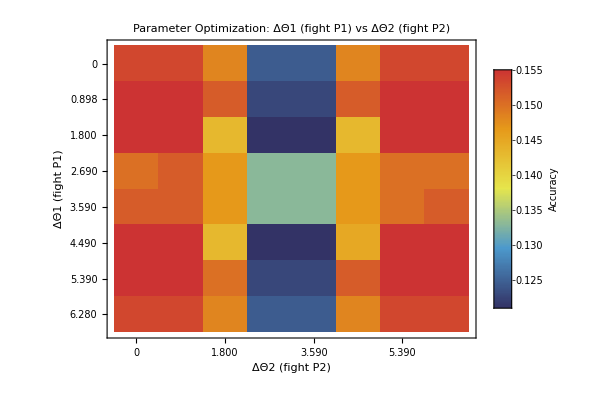

```mathematica
visualizeGridSearchResults4D[gridResults,{1,2}]
```

```mathematica
plotQuantumNormalFormConfusionMatrix[bestResults,bestDeltaTheta1,bestDeltaTheta2,bestDeltaTheta3,bestDeltaTheta4,l1,l2,"Quantum Normal Form Model - Best Parameters"]
```

Quantum Normal Form Model - Best Parameters

ΔΘ1 = 0 ΔΘ2 = 2 Pi
----
 7 ΔΘ3 = 0 ΔΘ4 = 2 Pi
----
 7 λ1 = 1 λ2 = 1 | Accuracy = 0.15544

Actual \ Predicted | ACQ1 | ACQ2 | CAP1 | CAP2 | NEGO | SQ | WAR1
ACQ1 | 0 | 1 | 0 | 0 | 0 | 3 | 2
ACQ2 | 19 | 54 | 0 | 0 | 0 | 6 | 20
CAP1 | 8 | 24 | 0 | 0 | 0 | 3 | 21
CAP2 | 24 | 48 | 0 | 0 | 0 | 4 | 23
NEGO | 21 | 30 | 0 | 0 | 0 | 13 | 35
SQ | 37 | 33 | 0 | 0 | 0 | 8 | 21
WAR1 | 20 | 43 | 0 | 0 | 0 | 8 | 28

#### Setting 2: Lambda1 = 0.5 | Lambda2 = 0.5

```mathematica
datasetPath =  "D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";
data=loadData[datasetPath];
```

Loading CSV file: D:\home\Documents\Github\quantum_international_interaction_game\dataset\balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
gridsize = 8;
l1 =0.5;
l2=0.5;
deltaTheta1Range=createThetaRange[0,2*Pi,gridsize];
deltaTheta2Range=createThetaRange[0,2*Pi,gridsize];
deltaTheta3Range=createThetaRange[0,2*Pi,gridsize];
deltaTheta4Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumNormalFormThetas[data,deltaTheta1Range,deltaTheta2Range,deltaTheta3Range,deltaTheta4Range,l1,l2,False ];
```

```mathematica
Print["\n=== GRID SEARCH RESULTS ==="];
Print["Best parameters found:"];
Print["  DeltaTheta1 (fight P1) = ",gridResults["bestDeltaTheta1"]];
Print["  DeltaTheta2 (fight P2) = ",gridResults["bestDeltaTheta2"]];
Print["  DeltaTheta3 (demand P1) = ",gridResults["bestDeltaTheta3"]];
Print["  DeltaTheta4 (demand P2) = ",gridResults["bestDeltaTheta4"]];
Print["  Best accuracy = ",gridResults["bestAccuracy"]];
```

```mathematica
bestDeltaTheta1=gridResults["bestDeltaTheta1"];
bestDeltaTheta2=gridResults["bestDeltaTheta2"];
bestDeltaTheta3=gridResults["bestDeltaTheta3"];
bestDeltaTheta4=gridResults["bestDeltaTheta4"];
```

```mathematica
bestResults=processQuantumNormalFormDataset[data,bestDeltaTheta1,bestDeltaTheta2,bestDeltaTheta3,bestDeltaTheta4,l1,l2,True];
```

```mathematica
finalAccuracy=calculateQuantumNormalFormAccuracy[bestResults];
Print["Final accuracy with best parameters: ",N[finalAccuracy,4]];
```

```mathematica
sampleResults=getFirstNEntries[bestResults,3]
```

```mathematica
visualizeGridSearchResults4D[gridResults,{1,2}]
```

```mathematica
plotQuantumNormalFormConfusionMatrix[bestResults,bestDeltaTheta1,bestDeltaTheta2,bestDeltaTheta3,bestDeltaTheta4,l1,l2,"Quantum Normal Form Model - Best Parameters"]
```

#### Setting 3: Lambda1 = 2 | Lambda2 = 2

```mathematica
datasetPath =  "D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";
data=loadData[datasetPath];
```

Loading CSV file: D:\home\Documents\Github\quantum_international_interaction_game\dataset\balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
gridsize = 8;
l1 =2;
l2=2;
deltaTheta1Range=createThetaRange[0,2*Pi,gridsize];
deltaTheta2Range=createThetaRange[0,2*Pi,gridsize];
deltaTheta3Range=createThetaRange[0,2*Pi,gridsize];
deltaTheta4Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumNormalFormThetas[data,deltaTheta1Range,deltaTheta2Range,deltaTheta3Range,deltaTheta4Range,l1,l2,False ];
```

```mathematica
Print["\n=== GRID SEARCH RESULTS ==="];
Print["Best parameters found:"];
Print["  DeltaTheta1 (fight P1) = ",gridResults["bestDeltaTheta1"]];
Print["  DeltaTheta2 (fight P2) = ",gridResults["bestDeltaTheta2"]];
Print["  DeltaTheta3 (demand P1) = ",gridResults["bestDeltaTheta3"]];
Print["  DeltaTheta4 (demand P2) = ",gridResults["bestDeltaTheta4"]];
Print["  Best accuracy = ",gridResults["bestAccuracy"]];
```

```mathematica
bestDeltaTheta1=gridResults["bestDeltaTheta1"];
bestDeltaTheta2=gridResults["bestDeltaTheta2"];
bestDeltaTheta3=gridResults["bestDeltaTheta3"];
bestDeltaTheta4=gridResults["bestDeltaTheta4"];
```

```mathematica
bestResults=processQuantumNormalFormDataset[data,bestDeltaTheta1,bestDeltaTheta2,bestDeltaTheta3,bestDeltaTheta4,l1,l2,True];
```

```mathematica
finalAccuracy=calculateQuantumNormalFormAccuracy[bestResults];
Print["Final accuracy with best parameters: ",N[finalAccuracy,4]];
```

```mathematica
sampleResults=getFirstNEntries[bestResults,3]
```

```mathematica
visualizeGridSearchResults4D[gridResults,{1,2}]
```

```mathematica
plotQuantumNormalFormConfusionMatrix[bestResults,bestDeltaTheta1,bestDeltaTheta2,bestDeltaTheta3,bestDeltaTheta4,l1,l2,"Quantum Normal Form Model - Best Parameters"]
```

#### Setting 4: Lambda1 = 0.1 | Lambda2 = 0.1

```mathematica
datasetPath =  "D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";
data=loadData[datasetPath];
```

Loading CSV file: D:\home\Documents\Github\quantum_international_interaction_game\dataset\balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
gridsize = 8;
l1 =0.1;
l2= 0.1;
deltaTheta1Range=createThetaRange[0,2*Pi,gridsize];
deltaTheta2Range=createThetaRange[0,2*Pi,gridsize];
deltaTheta3Range=createThetaRange[0,2*Pi,gridsize];
deltaTheta4Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumNormalFormThetas[data,deltaTheta1Range,deltaTheta2Range,deltaTheta3Range,deltaTheta4Range,l1,l2,False ];
```

```mathematica
Print["\n=== GRID SEARCH RESULTS ==="];
Print["Best parameters found:"];
Print["  DeltaTheta1 (fight P1) = ",gridResults["bestDeltaTheta1"]];
Print["  DeltaTheta2 (fight P2) = ",gridResults["bestDeltaTheta2"]];
Print["  DeltaTheta3 (demand P1) = ",gridResults["bestDeltaTheta3"]];
Print["  DeltaTheta4 (demand P2) = ",gridResults["bestDeltaTheta4"]];
Print["  Best accuracy = ",gridResults["bestAccuracy"]];
```

```mathematica
bestDeltaTheta1=gridResults["bestDeltaTheta1"];
bestDeltaTheta2=gridResults["bestDeltaTheta2"];
bestDeltaTheta3=gridResults["bestDeltaTheta3"];
bestDeltaTheta4=gridResults["bestDeltaTheta4"];
```

```mathematica
bestResults=processQuantumNormalFormDataset[data,bestDeltaTheta1,bestDeltaTheta2,bestDeltaTheta3,bestDeltaTheta4,l1,l2,True];
```

```mathematica
finalAccuracy=calculateQuantumNormalFormAccuracy[bestResults];
Print["Final accuracy with best parameters: ",N[finalAccuracy,4]];
```

```mathematica
sampleResults=getFirstNEntries[bestResults,3]
```

```mathematica
visualizeGridSearchResults4D[gridResults,{1,2}]
```

```mathematica
plotQuantumNormalFormConfusionMatrix[bestResults,bestDeltaTheta1,bestDeltaTheta2,bestDeltaTheta3,bestDeltaTheta4,l1,l2,"Quantum Normal Form Model - Best Parameters"]
```

#### Setting 5: Lambda1 = 10 | Lambda2 = 10

```mathematica
datasetPath =  "D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";
data=loadData[datasetPath];
```

Loading CSV file: D:\home\Documents\Github\quantum_international_interaction_game\dataset\balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
gridsize = 8;
l1 =10;
l2=10;
deltaTheta1Range=createThetaRange[0,2*Pi,gridsize];
deltaTheta2Range=createThetaRange[0,2*Pi,gridsize];
deltaTheta3Range=createThetaRange[0,2*Pi,gridsize];
deltaTheta4Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumNormalFormThetas[data,deltaTheta1Range,deltaTheta2Range,deltaTheta3Range,deltaTheta4Range,l1,l2,False ];
```

```mathematica
Print["\n=== GRID SEARCH RESULTS ==="];
Print["Best parameters found:"];
Print["  DeltaTheta1 (fight P1) = ",gridResults["bestDeltaTheta1"]];
Print["  DeltaTheta2 (fight P2) = ",gridResults["bestDeltaTheta2"]];
Print["  DeltaTheta3 (demand P1) = ",gridResults["bestDeltaTheta3"]];
Print["  DeltaTheta4 (demand P2) = ",gridResults["bestDeltaTheta4"]];
Print["  Best accuracy = ",gridResults["bestAccuracy"]];
```

```mathematica
bestDeltaTheta1=gridResults["bestDeltaTheta1"];
bestDeltaTheta2=gridResults["bestDeltaTheta2"];
bestDeltaTheta3=gridResults["bestDeltaTheta3"];
bestDeltaTheta4=gridResults["bestDeltaTheta4"];
```

```mathematica
bestResults=processQuantumNormalFormDataset[data,bestDeltaTheta1,bestDeltaTheta2,bestDeltaTheta3,bestDeltaTheta4,l1,l2,True];
```

```mathematica
finalAccuracy=calculateQuantumNormalFormAccuracy[bestResults];
Print["Final accuracy with best parameters: ",N[finalAccuracy,4]];
```

```mathematica
sampleResults=getFirstNEntries[bestResults,3]
```

```mathematica
visualizeGridSearchResults4D[gridResults,{1,2}]
```

```mathematica
plotQuantumNormalFormConfusionMatrix[bestResults,bestDeltaTheta1,bestDeltaTheta2,bestDeltaTheta3,bestDeltaTheta4,l1,l2,"Quantum Normal Form Model - Best Parameters"]
```

#### Setting 6: Lambda1 = 0.0001 | Lambda2 = 0.0001

```mathematica
datasetPath =  "D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";
data=loadData[datasetPath];
```

Loading CSV file: D:\home\Documents\Github\quantum_international_interaction_game\dataset\balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
gridsize = 8;
l1 =0.0001;
l2=0.0001;
deltaTheta1Range=createThetaRange[0,2*Pi,gridsize];
deltaTheta2Range=createThetaRange[0,2*Pi,gridsize];
deltaTheta3Range=createThetaRange[0,2*Pi,gridsize];
deltaTheta4Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumNormalFormThetas[data,deltaTheta1Range,deltaTheta2Range,deltaTheta3Range,deltaTheta4Range,l1,l2,False ];
```

```mathematica
Print["\n=== GRID SEARCH RESULTS ==="];
Print["Best parameters found:"];
Print["  DeltaTheta1 (fight P1) = ",gridResults["bestDeltaTheta1"]];
Print["  DeltaTheta2 (fight P2) = ",gridResults["bestDeltaTheta2"]];
Print["  DeltaTheta3 (demand P1) = ",gridResults["bestDeltaTheta3"]];
Print["  DeltaTheta4 (demand P2) = ",gridResults["bestDeltaTheta4"]];
Print["  Best accuracy = ",gridResults["bestAccuracy"]];
```

```mathematica
bestDeltaTheta1=gridResults["bestDeltaTheta1"];
bestDeltaTheta2=gridResults["bestDeltaTheta2"];
bestDeltaTheta3=gridResults["bestDeltaTheta3"];
bestDeltaTheta4=gridResults["bestDeltaTheta4"];
```

```mathematica
bestResults=processQuantumNormalFormDataset[data,bestDeltaTheta1,bestDeltaTheta2,bestDeltaTheta3,bestDeltaTheta4,l1,l2,True];
```

```mathematica
finalAccuracy=calculateQuantumNormalFormAccuracy[bestResults];
Print["Final accuracy with best parameters: ",N[finalAccuracy,4]];
```

```mathematica
sampleResults=getFirstNEntries[bestResults,3]
```

```mathematica
visualizeGridSearchResults4D[gridResults,{1,2}]
```

```mathematica
plotQuantumNormalFormConfusionMatrix[bestResults,bestDeltaTheta1,bestDeltaTheta2,bestDeltaTheta3,bestDeltaTheta4,l1,l2,"Quantum Normal Form Model - Best Parameters"]
```